## This is meant to be the nb to see if we can generalize our action to describe the b-LRW. To make the Code leaner, I want to use a .m file with the definition of functions and then use a nb to “compile” it.

```mathematica
Quiet[<<(FileNameJoin[{NotebookDirectory[],"b-LRW-Update.m"}])]
```

# Automated solver of the Laplace equation

## LaplaceEqSolver[]

```mathematica
Clear[LaplaceEqSolver];
Options[LaplaceEqSolver]={"BC"->{{},{}} , "selectSolution"->0};

LaplaceEqSolver[graph_,OptionsPattern[]]:=Module[{locVertices,locWeights,totWeights,locRoot,locSource,locBC,equations,variables={},x,solution},
Clear[Φ];

locVertices = VertexList@graph;
locWeights=WeightedAdjacencyMatrix[graph]//Normal;
totWeights =Total[locWeights,{2}];

locRoot = 
 Select[(List@@@PropertyValue[graph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"ROOT"]&][[All,1]][[1]];
locSource = 
 Select[(List@@@PropertyValue[graph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"SOURCE"]&][[All,1]][[1]];

locBC=OptionValue["BC"];

If[locBC=!={{},{}},

AppendTo[locBC[[1]],Φ[locSource]== 1];
AppendTo[locBC[[1]],Φ[locRoot]==0];

AppendTo[locBC[[2]],locSource];
AppendTo[locBC[[2]],locRoot];
];

equations =locBC[[1]] ;

For[x=1,x<=Length[locVertices],x++,
AppendTo[variables,Φ[x]];
If[MemberQ[locBC[[2]],x],Continue[]];
AppendTo[equations, Φ[x]==FullSimplify[Sum[locWeights[[x,y]]/totWeights[[x]] Φ[y],{y,Length[locVertices]}]]]];
(*Print[equations];
Print[variables];*)
solution=Flatten@Solve[equations,variables]/.Rule->List;

If[OptionValue["selectSolution"]!=0,(*True*)
solution=Select[solution,#[[1]]==Φ[OptionValue["selectSolution"]] &][[1,2]]
];

Return[solution]
]
```

### Usage example of LaplaceEqSolver[]

“boundaryConditions” should be a 2d list with the boundary conditions given as a first list, e.g. {ϕ[1] == 1, ϕ[2] == 0}. The second list must contain the vertices in the boundary, e.g. {1, 2}

```mathematica
g
```

g

```mathematica
BC={{Φ[4]==1},{4}};
path1={{1,5},{5,4}};
sol=LaplaceEqSolver[g,"BC"->BC]/.β[__]->1
```

PropertyValue::pvobj: g is not an object with properties.

PropertyValue::argr: PropertyValue called with 1 argument; 2 arguments are expected.

Part::partd: Part specification VertexLabels⟦2⟧ is longer than depth of object.

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[VertexLabels⟦2⟧,___~~ROOT].

PropertyValue::argrx: PropertyValue called with 0 arguments; 2 arguments are expected.

Part::partw: Part 1 of PropertyValue[] does not exist.

PropertyValue::pvobj: g is not an object with properties.

PropertyValue::argr: PropertyValue called with 1 argument; 2 arguments are expected.

Part::partd: Part specification VertexLabels⟦2⟧ is longer than depth of object.

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[VertexLabels⟦2⟧,___~~SOURCE].

PropertyValue::argrx: PropertyValue called with 0 arguments; 2 arguments are expected.

General::stop: Further output of PropertyValue::argrx will be suppressed during this calculation.

Part::partw: Part 1 of PropertyValue[] does not exist.

Part::partd: Part specification WeightedAdjacencyMatrix[g]⟦1,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{}

```mathematica
BC={{Φ[4]==1},{4}};
path1={{1,5},{5,4}};
sol=LaplaceEqSolver[g,"BC"->BC]
Select[sol,#[[1]]==Φ[path1[[1,2]]] &][[1,2]];

sol=LaplaceEqSolver[g,"selectSolution"->1]
```

PropertyValue::pvobj: g is not an object with properties.

PropertyValue::argr: PropertyValue called with 1 argument; 2 arguments are expected.

Part::partd: Part specification VertexLabels⟦2⟧ is longer than depth of object.

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[VertexLabels⟦2⟧,___~~ROOT].

PropertyValue::argrx: PropertyValue called with 0 arguments; 2 arguments are expected.

Part::partw: Part 1 of PropertyValue[] does not exist.

PropertyValue::pvobj: g is not an object with properties.

PropertyValue::argr: PropertyValue called with 1 argument; 2 arguments are expected.

Part::partd: Part specification VertexLabels⟦2⟧ is longer than depth of object.

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[VertexLabels⟦2⟧,___~~SOURCE].

PropertyValue::argrx: PropertyValue called with 0 arguments; 2 arguments are expected.

General::stop: Further output of PropertyValue::argrx will be suppressed during this calculation.

Part::partw: Part 1 of PropertyValue[] does not exist.

Part::partd: Part specification WeightedAdjacencyMatrix[g]⟦1,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{}

Part::partw: Part 1 of {} does not exist.

PropertyValue::pvobj: g is not an object with properties.

PropertyValue::argr: PropertyValue called with 1 argument; 2 arguments are expected.

Part::partd: Part specification VertexLabels⟦2⟧ is longer than depth of object.

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[VertexLabels⟦2⟧,___~~ROOT].

PropertyValue::argrx: PropertyValue called with 0 arguments; 2 arguments are expected.

Part::partw: Part 1 of PropertyValue[] does not exist.

PropertyValue::pvobj: g is not an object with properties.

PropertyValue::argr: PropertyValue called with 1 argument; 2 arguments are expected.

Part::partd: Part specification VertexLabels⟦2⟧ is longer than depth of object.

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[VertexLabels⟦2⟧,___~~SOURCE].

PropertyValue::argrx: PropertyValue called with 0 arguments; 2 arguments are expected.

General::stop: Further output of PropertyValue::argrx will be suppressed during this calculation.

Part::partw: Part 1 of PropertyValue[] does not exist.

Part::partd: Part specification WeightedAdjacencyMatrix[g]⟦1,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

0

```mathematica
Solve[{Φ[3]==1,Φ[1]==0,Φ[2]==1/3(Φ[1]+Φ[3]+Φ[4]),Φ[4]==1/2(Φ[2]+Φ[3])},{Φ[1],Φ[2],Φ[3],Φ[4]}]
```

{{Φ[1]→0,Φ[2]→3/5,Φ[3]→1,Φ[4]→4/5}}

Let’s keep the value at the source general. The idea is that we want to use it to impose the normalization such that ϕ are already properly normalized for being transition probabilities.

```mathematica
BC={{Φ[3]==Zeta[3],Φ[2]==0},{3,2}};
path1={{2,1},{1,3}};
sol=LaplaceEqSolver[g,BC,Φ]
```

LaplaceEqSolver[g,{{Φ[3]==Zeta[3],Φ[2]==0},{3,2}},Φ]

As you can see from the previous example, the source’s value appear at numerator. So, we need to instead take its inverse. THE CRUCIAL THING IS THAT IT IS EXTREMELY EASY TO TAKE THE INVERSE OF A NUMBER, COMPARED TO THE INVERSE OF AN EXPECTATION VALUE!!!!!

## bLaplacianRW[]

Computes the probability of a given Laplacian RW

```mathematica
Clear[bLaplacianRW];
Options[bLaplacianRW]={"draw"->False,"print"->False};
bLaplacianRW[graph_,path__,b_,OptionsPattern[]]:=Module[{locSource,locRoot,locWeights,locVertices,denominator,prob=1},
locWeights=WeightedAdjacencyMatrix[graph]/.β[__]->1//Normal;
locVertices=VertexList@graph;
locRoot = 
 Select[(List@@@PropertyValue[graph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"ROOT"]&][[All,1]][[1]];
locSource = 
 Select[(List@@@PropertyValue[graph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"SOURCE"]&][[All,1]][[1]];

If[locRoot =!= path[[1,1]], Print["####  WRONG ROOT  ####"]; Abort[]];
If[locSource =!= path[[-1,2]], Print["####  WRONG SOURCE  ####"];Abort[]];

Module[{locBC={{},{}},ϕ,i,ϕsol},

AppendTo[locBC[[1]],Φ[locSource]==1];
AppendTo[locBC[[2]],locSource];

For[i=1,i<=Length[path],i++,
AppendTo[locBC[[1]],Φ[path[[i,1]]]==0];
AppendTo[locBC[[2]],path[[i,1]]];

(*Print[locBC];*)

ϕsol=LaplaceEqSolver[graph,"BC"->locBC]/.β[__]->1;
(*Print[ϕsol];*)

(*Print[" ##### OK SO FAR ##### "];*)

denominator=Sum[locWeights[[path[[i,1]],y]]*(Select[ϕsol,#[[1]]==Φ[y] &][[1,2]])^b,{y,Length[locVertices]}];
(*Print[denominator]*);

If[OptionValue["print"],
Print["#####  Transition probability "<>ToString[path[[i,1]]]<>" to "<>ToString[path[[i,2]]]<>"  #####"];

Print[(locWeights[[path[[i,1]],path[[i,2]]]]*(Select[ϕsol,#[[1]]==Φ[path[[i,2]]] &][[1,2]])^b)/denominator/.β[_,_]->1//FullSimplify];
];

prob*=(locWeights[[path[[i,1]],path[[i,2]]]]*(Select[ϕsol,#[[1]]==Φ[path[[i,2]]] &][[1,2]])^b)/denominator/.β[__]->1//FullSimplify;
Clear[ϕsol];
];(*END OF FOR*)
];(*END OF MODULE*)

If[OptionValue["draw"],Print[DrawOnGraph[graph,path]]];
Return[prob]
]
```

Let’s write a modified LaplacianRW function that uses the normalization trick to normalize the transition probability. The only problem is the first step, so we compute it separately using the standard procedure.

(****************************************************************************************************************************)
NOT SO EASY, PLEASE LOOK AT IT MORE CAREFULLY. IN PARTICULAR WE NEED TO DIVIDE BY THE PARTITION FUNCTION!!!!!
So, we need to use a partition function calculator. I am trying to implement it in another notebook following Kay’s advice. But I am not able to reproduce it. So, since its program is just an optimization, I will use mine and think about how to improve it in the future.
(****************************************************************************************************************************)

```mathematica
Clear[LaplacianRW2];
Options[LaplacianRW2]={"draw"->False,"print"->False};

LaplacianRW2[graph_,path__,OptionsPattern[]]:=Module[{locSource,locRoot,locWeights,totWeights,locVertices,denominator,prob=1, Z,numerator},
locWeights=WeightedAdjacencyMatrix[graph]//Normal;
totWeights =Total[locWeights,{2}];

locVertices=VertexList@graph;

locRoot = 
 Select[(List@@@PropertyValue[graph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"ROOT"]&][[All,1]][[1]];
locSource = 
 Select[(List@@@PropertyValue[graph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"SOURCE"]&][[All,1]][[1]];

If[locRoot =!= path[[1,1]], Print["####  WRONG ROOT  ####"]; Return[NULL]];
If[locSource =!= path[[-1,2]], Print["####  WRONG SOURCE  ####"];Return[NULL]];

Module[{locBC={{},{}},ϕ,i=1,j,ϕsol},
AppendTo[locBC[[1]],ϕ[locSource]==1];
AppendTo[locBC[[2]],locSource];

AppendTo[locBC[[1]],ϕ[path[[i,1]]]==0];
AppendTo[locBC[[2]],path[[i,1]]];

ϕsol=LaplaceEqSolver[graph,locBC,ϕ];
(*Print[ϕsol]*);

denominator=Sum[locWeights[[path[[i,1]],y]]*Select[ϕsol,#[[1]]==ϕ[y] &][[1,2]],{y,Length[locVertices]}];
(*Print[denominator]*);

numerator=locWeights[[path[[i,1]],path[[i,2]]]] * Select[ϕsol,#[[1]]==ϕ[path[[i,2]]] &][[1,2]]//FullSimplify;

prob*=numerator/denominator//FullSimplify;

Print["#####  Transition probability "<>ToString[path[[i,1]]]<>" to "<>ToString[path[[i,2]]]<>"  #####"];
Print[prob/.β[_,_]->1//FullSimplify];

Clear[ϕsol,locBC];

For[i=2,i<=Length[path],i++,
(*We need to solve it once with standard BCs at the previous step, i.e. ϕ[locSource]==1*)
locBC={{ϕ[locSource]==1},{locSource}};

For[j=1,j<=i-1,j++,
AppendTo[locBC[[1]],ϕ[path[[j,1]]]==0];
AppendTo[locBC[[2]],path[[j,1]]]
]

(*Print[locBC]*);

Z=VertexAssignment[graph, "excludedVertices"->locBC[[2]]];
Z=ExpectationValue[Z];

If[OptionValue["print"],
Print["#####  Previous Partition Function  #####"];
Print[Z]
];

ϕsol=LaplaceEqSolver[graph,locBC,ϕ];
(*Print[ϕsol];*)

denominator=1/Z*Select[ϕsol,#[[1]]==ϕ[path[[i,1]]] &][[1,2]]//FullSimplify;

Clear[ϕsol, locBC];


(*Then we need to solve it again with updated BC at the current step*)
locBC={{ϕ[locSource]==denominator^-1},{locSource}};

For[j=1,j<=i,j++,
AppendTo[locBC[[1]],ϕ[path[[j,1]]]==0];
AppendTo[locBC[[2]],path[[j,1]]]
]

(*Print[locBC]*);

Z=VertexAssignment[graph, "excludedVertices"->locBC[[2]]];
Z=ExpectationValue[Z];

If[OptionValue["print"],
Print["#####  Current Partition Function  #####"];
Print[Z]
];

ϕsol=LaplaceEqSolver[graph,locBC,ϕ];
(*Print[ϕsol]*);

Print["#####  Transition probability "<>ToString[path[[i,1]]]<>" to "<>ToString[path[[i,2]]]<>"  #####"];
Print[1/Z*locWeights[[path[[i,1]],path[[i,2]]]]/totWeights[[path[[i,1]]]]*Select[ϕsol,#[[1]]==ϕ[path[[i,2]]] &][[1,2]]/.β[_,_]->1//FullSimplify];

prob*=1/Z*locWeights[[path[[i,1]],path[[i,2]]]]/totWeights[[path[[i,1]]]]*Select[ϕsol,#[[1]]==ϕ[path[[i,2]]] &][[1,2]]//FullSimplify;

Clear[ϕsol,locBC];
]
];
If[OptionValue["draw"],Print[DrawOnGraph[graph,path]]];
Return[prob]
]
```

### Test bLaplacianRW[]

```mathematica
g
```

g

```mathematica
path={{1,5},{5,4}};
b=2;
bLaplacianRW[g,path,b]
```

PropertyValue::pvobj: g is not an object with properties.

PropertyValue::argr: PropertyValue called with 1 argument; 2 arguments are expected.

Part::partd: Part specification VertexLabels⟦2⟧ is longer than depth of object.

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[VertexLabels⟦2⟧,___~~ROOT].

PropertyValue::argrx: PropertyValue called with 0 arguments; 2 arguments are expected.

Part::partw: Part 1 of PropertyValue[] does not exist.

PropertyValue::pvobj: g is not an object with properties.

PropertyValue::argr: PropertyValue called with 1 argument; 2 arguments are expected.

Part::partd: Part specification VertexLabels⟦2⟧ is longer than depth of object.

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[VertexLabels⟦2⟧,___~~SOURCE].

PropertyValue::argrx: PropertyValue called with 0 arguments; 2 arguments are expected.

General::stop: Further output of PropertyValue::argrx will be suppressed during this calculation.

Part::partw: Part 1 of PropertyValue[] does not exist.

####  WRONG ROOT  ####

$Aborted

## PathFinder[]

```mathematica
Clear[PathFinder];

PathFinder[graph_]:=Module[{pathList={{}}},
Step[subgraph_]:=Module[{locEdges,locVertices,locWeights,locRoot,locSource,locMoves,newEdges, newRoot,smallerGraph,i},
locEdges = EdgeList@subgraph/.DirectedEdge->List;
locVertices=VertexList@subgraph;
If[Length[locVertices]==1,Return[NULL]];
locWeights=WeightedAdjacencyMatrix[subgraph]//Normal;
locRoot = 
 Select[(List@@@PropertyValue[subgraph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"ROOT"]&][[All,1]][[1]];
locSource = 
 Select[(List@@@PropertyValue[subgraph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"SOURCE"]&][[All,1]][[1]];
locMoves=Select[locEdges,#[[1]]==locRoot &][[All]];

(*Print["###  LocMoves  ####"];
Print[locMoves];*);

For[i=1, i<=Length[locMoves],i++,

If[i ==Length[locMoves],
(*True*)If[locMoves[[i,2]]==locSource,
 (*Ture*)pathList=Append[pathList[[2;;]],Append[pathList[[1]],locMoves[[i]]]]; Continue[],
 (*False*)pathList=Prepend[pathList[[2;;]],Append[pathList[[1]],locMoves[[i]]]]
],
(*False*)
If[locMoves[[i,2]]==locSource,
 (*True*)pathList=Append[pathList,Append[pathList[[1]],locMoves[[i]]]];Continue[],
 (*False*)pathList=Prepend[pathList,Append[pathList[[1]],locMoves[[i]]]]
]];

(*Print["###  pathList  ####"];
Print[pathList];*);

newEdges=Select[locEdges,#[[1]]=!=locRoot && #[[2]]=!=locRoot &][[All]];
newRoot = locMoves[[i,2]];
If[Length[newEdges] <= 0,Continue[]];
smallerGraph=MyGraph[newEdges,newRoot,locSource,"undirected"->False][[1]];

(*Print[smallerGraph];*);

Step[smallerGraph]
]
];

Step[graph];
Return[pathList]
]
```

### Usage example of PathFinder[]

```mathematica
g
PathFinder[g]
```

g

{{}}

So

```mathematica
(*Last step available*)
v=Prepend[v[[2;;]],Append[v[[1]],step0]]
```

Part::take: Cannot take positions 2 through -1 in v.

Part::partd: Part specification v⟦1⟧ is longer than depth of object.

Part::pkspec1: The expression step0 cannot be used as a part specification.

Part::pkspec1: The expression v cannot be used as a part specification.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

Part::pkspec1: The expression step0 cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

TerminatedEvaluation[RecursionLimit]⟦1,step0⟧⟦TerminatedEvaluation[RecursionLimit],2;;All⟧

```mathematica
(*Multiple steps available*)
v=Prepend[v,Append[v[[1]],step1]]
```

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

Part::pkspec1: The expression step0 cannot be used as a part specification.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

Part::pkspec1: The expression TerminatedEvaluation[RecursionLimit] cannot be used as a part specification.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit::reclim will be suppressed during this calculation.

Part::pkspec1: The expression step0 cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

TerminatedEvaluation[RecursionLimit]⟦1,step0,step1⟧⟦TerminatedEvaluation[RecursionLimit]⟦1,step0⟧,TerminatedEvaluation[RecursionLimit],2;;All⟧

```mathematica
(*Source reached with last step available*)
v=Append[v[[2;;]],Append[v[[1]],step2]]
```

Part::pkspec1: The expression TerminatedEvaluation[RecursionLimit] cannot be used as a part specification.

Part::pkspec1: The expression step0 cannot be used as a part specification.

Part::pkspec1: The expression TerminatedEvaluation[RecursionLimit] cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

TerminatedEvaluation[RecursionLimit]⟦1,step0⟧⟦TerminatedEvaluation[RecursionLimit],2;;All,TerminatedEvaluation[RecursionLimit]⟦1,step0,step1,step2⟧⟧

```mathematica
(*Source reached with multiple steps available*)
v=Append[v,Append[v[[1]],step2]]
```

Part::pkspec1: The expression step0 cannot be used as a part specification.

Part::pkspec1: The expression TerminatedEvaluation[RecursionLimit] cannot be used as a part specification.

TerminatedEvaluation[RecursionLimit]⟦1,step0⟧⟦TerminatedEvaluation[RecursionLimit],2;;All,TerminatedEvaluation[RecursionLimit]⟦1,step0,step1,step2⟧,TerminatedEvaluation[RecursionLimit]⟦1,step0,step2⟧⟧

Test

```mathematica
Clear[a];
(*The first position is the one we are gonna update*)
v={{}}
rooot=a;
v=Prepend[v[[2;;]],Append[v[[1]],rooot]]
step0=b;(*If b is the only step available, then we do not need a copy of v*)
v=Prepend[v[[2;;]],Append[v[[1]],step0]]
step1=c;(*Imagine we can now move to c or c2. We then need a copy of v to be able to come back at this bifurcation*)
v=Prepend[v,Append[v[[1]],step1]]
step2=d;(*If d reaches the source, then add it to the end*)
v=Append[v,Append[v[[1]],step2]]
step2bis=d2;(*If d2 is the only step available, then we do not need a copy of v*)
v=Prepend[v[[2;;]],Append[v[[1]],step2bis]]
step3=e;(*If e reaches the source, and is the only step available, add it at the end without copying v*)
v=Append[v[[2;;]],Append[v[[1]],step3]]
```

{{}}

{{a}}

{{a,2}}

{{a,2,c},{a,2}}

{{a,2,c},{a,2},{a,2,c,d}}

{{a,2,c,d2},{a,2},{a,2,c,d}}

{{a,2},{a,2,c,d},{a,2,c,d2,e}}

## AllbLaplacianRWs[]

```mathematica
Clear[AllbLaplacianRWs]

Options[AllbLaplacianRWs]={"draw"->False,"print"->False};

AllbLaplacianRWs[graph_,b_,OptionsPattern[]]:=Module[{possibleLRW,i,probabilityLRW={}},
possibleLRW=PathFinder[graph];
For[i=1, i<= Length[possibleLRW],i++,
AppendTo[probabilityLRW,bLaplacianRW[graph,possibleLRW[[i]],b,"draw"->OptionValue["draw"]]];

If[OptionValue["print"],Print[i,") Laplacian RW ",possibleLRW[[i]]," with probability " ,probabilityLRW[[i]]]
]
];
possibleLRW=
Replace[possibleLRW,{a_?NumberQ,c_?NumberQ}:>R[a,c,RGBColor[1, 0, 0]],3];
Return[{possibleLRW,probabilityLRW}]
]
```

### Usage example of AllLaplacianRWs[]

```mathematica
{3}/.a_?NumberQ:>0
```

{0}

```mathematica
{1,2}/.{a_?NumberQ,b_?NumberQ}:>R[a,b,RGBColor[1, 0, 0]]
```

R[1,2,RGBColor[1, 0, 0]]

```mathematica
g
```

g

```mathematica
b=2;
AllbLaplacianRWs[g,b,"draw"->False]
Total[%[[-1]]]
```

{{{R[1,2,RGBColor[1, 0, 0]],R[2,3,RGBColor[1, 0, 0]],R[3,4,RGBColor[1, 0, 0]]},{R[1,2,RGBColor[1, 0, 0]],R[2,5,RGBColor[1, 0, 0]],R[5,4,RGBColor[1, 0, 0]]},{R[1,5,RGBColor[1, 0, 0]],R[5,2,RGBColor[1, 0, 0]],R[2,3,RGBColor[1, 0, 0]],R[3,4,RGBColor[1, 0, 0]]},{R[1,5,RGBColor[1, 0, 0]],R[5,4,RGBColor[1, 0, 0]]}},{225/793,100/793,18/793,450/793}}

1

# b-Laplacian Random Walk

## δrules

```mathematica
ClearAll[Σδrule];
Σδrule={δ[a_,b_]^n_/;(!NumericQ[b]&& !MatchQ[b,Subscript[1, __]]):>δ[a,b]^(n-2)δ[a,a],
δ[b_,a_]δ[c_,b_]/;(!NumericQ[b] && !MatchQ[b,Subscript[1, __]]):>δ[c,a],
δ[a_,b_]δ[c_,b_]/;(!NumericQ[b]&& !MatchQ[b,Subscript[1, __]]):>δ[a,c],
δ[a_,a_]/;(MatchQ[a,Subscript[i, __]])/;(a=!=Subscript[i, s]):>n,
δ[a_,a_]/;(MatchQ[a,Subscript[j, __]])/;(a=!=Subscript[j, s]):>n,
δ[a_,a_]/;(MatchQ[a,Subscript[k, _]]):>1,
δ[a_,a_]/;(MatchQ[a,Subscript[l, _]]):>1,
δ[a_,a_]/;(MatchQ[a,Subscript[ll, _]]):>1};
```

```mathematica
ClearAll[δruleExternal];
δruleExternal={δ[a_,a_]/;(NumericQ[a] || a==Subscript[i, s] || MatchQ[a,Subscript[j, __]]|| MatchQ[a,Subscript[1, __]]|| MatchQ[a,Subscript[jjj, __]] ||MatchQ[a,Subscript[k, _]]):>1,
δ[a_,b_]/;(NumericQ[a] ||MatchQ[a,Subscript[k, _]]|| MatchQ[a,Subscript[j, __]]|| MatchQ[a,Subscript[1, _]]|| MatchQ[a,Subscript[jjj, __]] )/;(a=!=b):>0,
δ[a_,b_]/;(NumericQ[b] ||MatchQ[b,Subscript[k, _]]|| MatchQ[b,Subscript[j, __]]|| MatchQ[a,Subscript[1, _]]|| MatchQ[a,Subscript[jjj, __]] )/;(a=!=b):>0 };
```

## bLRWaction[] Benchmark

Let us try by calling the second copy another name, say ξ

```mathematica
Clear[bLRWaction];
Options[bLRWaction]={"sourceBC"->1,"excludedVertices"->{},"graph"->g,"startingTime"->1,"endTime"->10};

bLRWaction[OptionsPattern[]]:=Module[{locGraph,locStartingTime,locEndTime,locSource,locRoot,locWeights,totWeights,locVertices,actionTimeSlice,action},
Clear[i,k,j,γ];


locGraph=OptionValue["graph"];
locStartingTime =OptionValue["startingTime"];
locEndTime =OptionValue["endTime"];

locWeights=WeightedAdjacencyMatrix[locGraph]//Normal;
totWeights =Total[locWeights,{2}];

locVertices=VertexList@locGraph;

locRoot = 
 Select[(List@@@PropertyValue[locGraph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"ROOT"]&][[All,1]][[1]];
locSource = 
 Select[(List@@@PropertyValue[locGraph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"SOURCE"]&][[All,1]][[1]];


actionTimeSlice [T_]:= Product[
If[totWeights[[x]]===0  || MemberQ[OptionValue["excludedVertices"],x],1,
(*FALSE*)V[(γ Sum[locWeights[[x,y]](R[x,y,Red]ϕs[y,Subscript[t, T+1],Subscript[k, y]]ψs[x,Subscript[t, T+1],Subscript[ll, x]]-ϕs[x,Subscript[t, T+1],Subscript[k, x]])χs[y,Subscript[t, T],1]ξs[y,Subscript[t, T],1]*ϕ[x,Subscript[t, T],Subscript[k, x]],{y,Length[locVertices]}]+(1+Sum[locWeights[[x,y]]/totWeights[[x]] R[x,y,Blue]χs[y,Subscript[t, T],Subscript[i, x]]χ[x,Subscript[t, T],Subscript[i, x]],{y,Length[locVertices]}])(1+Sum[locWeights[[x,y]]/totWeights[[x]] R[x,y,Blue]ξs[y,Subscript[t, T],Subscript[j, x]]ξ[x,Subscript[t, T],Subscript[j, x]],{y,Length[locVertices]}])
+(*COPY ϕ*) ϕs[x,Subscript[t, T+1],Subscript[k, x]]*ϕ[x,Subscript[t, T],Subscript[k, x]]
+(*COPY ψ*) ψs[x,Subscript[t, T+1],Subscript[ll, x]]*ψ[x,Subscript[t, T],Subscript[ll, x]]) ]
],{x,Length[locVertices]}]
V[( ϕs[locSource,Subscript[t, T+1],Subscript[k, locSource]]ϕ[locSource,Subscript[t, T],Subscript[k, locSource]]+(1+χ[locSource,Subscript[t, T],1])*(1+ξ[locSource,Subscript[t, T],1]))];

action=Product[actionTimeSlice[T],{T,locEndTime}];

Return[action]

]
```

### bLRWnorm[]

```mathematica
Clear[bLRWnorm];
Options[bLRWnorm]={"graph"->g,"endTime"->endTime,"fieldsToExclude"->{ϕs,ψs},"theory"->"LERW","βrule"->{β[__]->1.},"fields"->FieldsNamesGenerator[{ϕ,χ,ξ,ψ}]};

bLRWnorm[expression_,OptionsPattern[]]:=Block[{locZnorm,excludedVertices,token,index},

excludedVertices=(expression * 2)/.R[__]->1/.γ->1//Expand;
excludedVertices=List @@excludedVertices;
excludedVertices=excludedVertices[[2;;]]; (*Gets rid of the numerical coefficient*)

For[index=1,index<=Length[OptionValue["fieldsToExclude"]],index++,
excludedVertices=excludedVertices/.OptionValue["fieldsToExclude"][[index]][a_,__]->a;
];
(*excludedVertices=excludedVertices/.ψs[a_,__]->a;
excludedVertices=excludedVertices/.ψs[a_,__]ψs[a_,__]->a;
excludedVertices=excludedVertices/.ξs[a_,__]->a;
excludedVertices=excludedVertices/.ξs[a_,__]ξs[a_,__]->a;*)

locZnorm=bLRWaction["graph"->g,"endTime"->OptionValue["endTime"],"excludedVertices"->excludedVertices]/.OptionValue["βrule"];(*VertexAssignment[OptionValue["graph"],"system"->"LERW","excludedVertices"->excludedVertices]/.OptionValue["βrule"];*)

ExpectationValueBlock[locZnorm *token,"endTime"->OptionValue["endTime"],"fields"->OptionValue["fields"],"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->OptionValue["graph"]]/.token->1
(*ExpectationValueBlock[locZnorm * token,"graph"->OptionValue["graph"],"fields"->FieldsNamesGenerator[{ϕ,χ,ξ}]]/.token->1*)
]
```

#### Test bLRWnorm[]

```mathematica
bLRWnorm[a,"graph"->g,"endTime"->endTime,"βrule"->{β[__]->1}]
```

479/432

```mathematica
bLRWnorm[ϕs[1,Subscript[t, 1],Subscript[k, 1]],"graph"->g,"endTime"->endTime,"βrule"->{β[__]->1}]
```

13/18

### Usage example of bLRWaction[]

My favorite graph

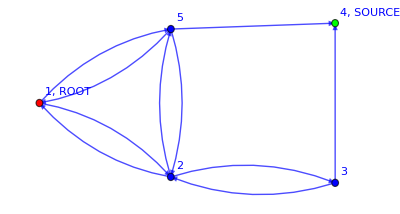

```mathematica
myFavoriteEdges={{1,2},{1,5},{2,3},{2,5},{5,4},{3,4}};
myFavoriteRoot=1;
myFavoriteSource=4;
myFavoriteGraph=MyGraph[myFavoriteEdges,myFavoriteRoot,myFavoriteSource][[1]]
```

Action assignment

```mathematica
g=myFavoriteGraph;
endTime=1;
Z=bLRWaction["graph"->g,"endTime"->endTime]/.β[__]->1;
Z0=Z/.γ->0;
```

```mathematica
Z
```

V[ϕ[4,t_1,k_4] ϕs[4,t_2,k_4]+(1+ξ[4,t_1,1]) (1+χ[4,t_1,1])] V[ϕ[1,t_1,k_1] ϕs[1,t_2,k_1]+(1+1/2 R[1,2,RGBColor[0, 0, 1]] ξ[1,t_1,j_1] ξs[2,t_1,j_1]+1/2 R[1,5,RGBColor[0, 0, 1]] ξ[1,t_1,j_1] ξs[5,t_1,j_1]) (1+1/2 R[1,2,RGBColor[0, 0, 1]] χ[1,t_1,i_1] χs[2,t_1,i_1]+1/2 R[1,5,RGBColor[0, 0, 1]] χ[1,t_1,i_1] χs[5,t_1,i_1])+ψ[1,t_1,ll_1] ψs[1,t_2,ll_1]+γ (ξs[2,t_1,1] ϕ[1,t_1,k_1] χs[2,t_1,1] (-ϕs[1,t_2,k_1]+R[1,2,RGBColor[1, 0, 0]] ϕs[2,t_2,k_2] ψs[1,t_2,ll_1])+ξs[5,t_1,1] ϕ[1,t_1,k_1] χs[5,t_1,1] (-ϕs[1,t_2,k_1]+R[1,5,RGBColor[1, 0, 0]] ϕs[5,t_2,k_5] ψs[1,t_2,ll_1]))] V[ϕ[2,t_1,k_2] ϕs[2,t_2,k_2]+(1+1/3 R[2,1,RGBColor[0, 0, 1]] ξ[2,t_1,j_2] ξs[1,t_1,j_2]+1/3 R[2,3,RGBColor[0, 0, 1]] ξ[2,t_1,j_2] ξs[3,t_1,j_2]+1/3 R[2,5,RGBColor[0, 0, 1]] ξ[2,t_1,j_2] ξs[5,t_1,j_2]) (1+1/3 R[2,1,RGBColor[0, 0, 1]] χ[2,t_1,i_2] χs[1,t_1,i_2]+1/3 R[2,3,RGBColor[0, 0, 1]] χ[2,t_1,i_2] χs[3,t_1,i_2]+1/3 R[2,5,RGBColor[0, 0, 1]] χ[2,t_1,i_2] χs[5,t_1,i_2])+ψ[2,t_1,ll_2] ψs[2,t_2,ll_2]+γ (ξs[1,t_1,1] ϕ[2,t_1,k_2] χs[1,t_1,1] (-ϕs[2,t_2,k_2]+R[2,1,RGBColor[1, 0, 0]] ϕs[1,t_2,k_1] ψs[2,t_2,ll_2])+ξs[3,t_1,1] ϕ[2,t_1,k_2] χs[3,t_1,1] (-ϕs[2,t_2,k_2]+R[2,3,RGBColor[1, 0, 0]] ϕs[3,t_2,k_3] ψs[2,t_2,ll_2])+ξs[5,t_1,1] ϕ[2,t_1,k_2] χs[5,t_1,1] (-ϕs[2,t_2,k_2]+R[2,5,RGBColor[1, 0, 0]] ϕs[5,t_2,k_5] ψs[2,t_2,ll_2]))] V[ϕ[3,t_1,k_3] ϕs[3,t_2,k_3]+(1+1/2 R[3,2,RGBColor[0, 0, 1]] ξ[3,t_1,j_3] ξs[2,t_1,j_3]+1/2 R[3,4,RGBColor[0, 0, 1]] ξ[3,t_1,j_3] ξs[4,t_1,j_3]) (1+1/2 R[3,2,RGBColor[0, 0, 1]] χ[3,t_1,i_3] χs[2,t_1,i_3]+1/2 R[3,4,RGBColor[0, 0, 1]] χ[3,t_1,i_3] χs[4,t_1,i_3])+ψ[3,t_1,ll_3] ψs[3,t_2,ll_3]+γ (ξs[2,t_1,1] ϕ[3,t_1,k_3] χs[2,t_1,1] (-ϕs[3,t_2,k_3]+R[3,2,RGBColor[1, 0, 0]] ϕs[2,t_2,k_2] ψs[3,t_2,ll_3])+ξs[4,t_1,1] ϕ[3,t_1,k_3] χs[4,t_1,1] (-ϕs[3,t_2,k_3]+R[3,4,RGBColor[1, 0, 0]] ϕs[4,t_2,k_4] ψs[3,t_2,ll_3]))] V[ϕ[5,t_1,k_5] ϕs[5,t_2,k_5]+(1+1/3 R[5,1,RGBColor[0, 0, 1]] ξ[5,t_1,j_5] ξs[1,t_1,j_5]+1/3 R[5,2,RGBColor[0, 0, 1]] ξ[5,t_1,j_5] ξs[2,t_1,j_5]+1/3 R[5,4,RGBColor[0, 0, 1]] ξ[5,t_1,j_5] ξs[4,t_1,j_5]) (1+1/3 R[5,1,RGBColor[0, 0, 1]] χ[5,t_1,i_5] χs[1,t_1,i_5]+1/3 R[5,2,RGBColor[0, 0, 1]] χ[5,t_1,i_5] χs[2,t_1,i_5]+1/3 R[5,4,RGBColor[0, 0, 1]] χ[5,t_1,i_5] χs[4,t_1,i_5])+ψ[5,t_1,ll_5] ψs[5,t_2,ll_5]+γ (ξs[1,t_1,1] ϕ[5,t_1,k_5] χs[1,t_1,1] (-ϕs[5,t_2,k_5]+R[5,1,RGBColor[1, 0, 0]] ϕs[1,t_2,k_1] ψs[5,t_2,ll_5])+ξs[2,t_1,1] ϕ[5,t_1,k_5] χs[2,t_1,1] (-ϕs[5,t_2,k_5]+R[5,2,RGBColor[1, 0, 0]] ϕs[2,t_2,k_2] ψs[5,t_2,ll_5])+ξs[4,t_1,1] ϕ[5,t_1,k_5] χs[4,t_1,1] (-ϕs[5,t_2,k_5]+R[5,4,RGBColor[1, 0, 0]] ϕs[4,t_2,k_4] ψs[5,t_2,ll_5]))]

#### Test that without contracting ξ we get the same as the LRW: YES

```mathematica
fields=FieldsNamesGenerator[{ϕ,χ,ψ}];
ExpectationValueBlock[Z ,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g,"nχ"->-1]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"/.ξ[__]->1/.ξs[__]->1//Expand
```

11/36

```mathematica
(*YES*)
```

#### Test that without contracting χ, but contracting ξ we get the same as the LRW: YES

```mathematica
fields=FieldsNamesGenerator[{ϕ,ξ,ψ}];
ExpectationValueBlock[Z ,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->False,"graph"->g,"nχ"->-1]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"/.χ[__]->1/.χs[__]->1//Expand
```

11/36

```mathematica
(*YES*)
```

#### Test that contracting ξ we get TWICE the LRW result: NO, WE DO NOT GET IT BECAUSE THERE ARE THE “MIXED” TERMS!!

```mathematica
fields=FieldsNamesGenerator[{ϕ,χ,ξ,ψ}];
ExpectationValueBlock[Z ,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->False,"graph"->g]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"(*/.ξ[__]->1/.ξs[__]->1*)//Expand
```

479/432

```mathematica
(* This is the right answer: we get more than just (11/36)^2 because we have the mixed terms!!*)
```

#### Test that it gives the solution to the Laplace equation to the power b

THIS HAS BEEN CHECKED BY COMMENTING OUT ξ!!!!!

E.g.  no BC OK

```mathematica
fields=FieldsNamesGenerator[{ϕ,χ,ψ}];
ExpectationValueBlock[Z0  ,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g](*/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"*)/.ξ[__]->1/.ξs[__]->1//Expand

ExpectationValueBlock[Z0 (*ψs[1,Subscript[t, 1],Subscript[ll, 1]]*) χs[5,Subscript[t, 1],1]ξs[5,Subscript[t, 1],1] ,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g](*/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"*)/.ξ[__]->1/.ξs[__]->1//Expand

%/%%
```

11/36

11/36

1

E.g. BC Φ(1)=0, implemented by ψ*(1)

and looking for Φ(5), implemented by χ*(5): OK

```mathematica
fields=FieldsNamesGenerator[{ϕ,χ,ψ}];
ExpectationValueBlock[Z0  ψs[1,Subscript[t, 1],Subscript[ll, 1]],"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g](*/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"*)/.ξ[__]->1/.ξs[__]->1//Expand

ExpectationValueBlock[Z0 ψs[1,Subscript[t, 1],Subscript[ll, 1]] χs[5,Subscript[t, 1],1]ξs[5,Subscript[t, 1],1] ,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g](*/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"*)/.ξ[__]->1/.ξs[__]->1//Expand

%/%%
```

13/18 ψs[1,t_2,ll_1]

1/3 ψs[1,t_2,ll_1]

6/13

```mathematica
(*OK*)
```

and looking for Φ(2), implemented by χ*(2): OK

```mathematica
fields=FieldsNamesGenerator[{ϕ,χ,ψ}];
ExpectationValueBlock[Z0  ψs[1,Subscript[t, 1],Subscript[ll, 1]],"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g](*/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"*)/.ξ[__]->1/.ξs[__]->1//Expand

ExpectationValueBlock[Z0 ψs[1,Subscript[t, 1],Subscript[ll, 1]] χs[2,Subscript[t, 1],1]ξs[5,Subscript[t, 1],1] ,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g](*/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"*)/.ξ[__]->1/.ξs[__]->1//Expand

%/%%
```

13/18 ψs[1,t_2,ll_1]

5/18 ψs[1,t_2,ll_1]

5/13

```mathematica
(*OK*)
```

Not contracting ξ  -> we get the same as LRW, i.e. b=1.	  ONLY WITH χ[locSource,t_T,1)*ξ[locSource,t_T,1]!!!!!1

E.g.  no BC

```mathematica
fields=FieldsNamesGenerator[{ϕ,χ,ψ}];
ExpectationValueBlock[Z0  ,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g](*/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"*)/.ξ[__]->1/.ξs[__]->1//Expand

ExpectationValueBlock[Z0 (*ψs[1,Subscript[t, 1],Subscript[ll, 1]]*) χs[5,Subscript[t, 1],1]ξs[5,Subscript[t, 1],1] ,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g](*/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"*)/.ξ[__]->1/.ξs[__]->1//Expand

%/%%
```

(11 V[2])/36

11/18

2/V[2]

E.g. BC Φ(1)=0, implemented by ψ*(1)

and looking for Φ(5), implemented by χ*(5):

```mathematica
fields=FieldsNamesGenerator[{ϕ,χ,ψ}];
ExpectationValueBlock[Z0  ψs[1,Subscript[t, 1],Subscript[ll, 1]],"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g](*/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"*)/.ξ[__]->1/.ξs[__]->1//Expand

ExpectationValueBlock[Z0 ψs[1,Subscript[t, 1],Subscript[ll, 1]] χs[5,Subscript[t, 1],1]ξs[5,Subscript[t, 1],1] ,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g](*/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"*)/.ξ[__]->1/.ξs[__]->1//Expand

%/%%
```

13/18 V[2] ψs[1,t_2,ll_1]

2/3 ψs[1,t_2,ll_1]

12/(13 V[2])

```mathematica
(*OK*)
```

and looking for Φ(2), implemented by χ*(2):

```mathematica
fields=FieldsNamesGenerator[{ϕ,χ,ψ}];
ExpectationValueBlock[Z0  ψs[1,Subscript[t, 1],Subscript[ll, 1]],"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g](*/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"*)/.ξ[__]->1/.ξs[__]->1//Expand

ExpectationValueBlock[Z0 ψs[1,Subscript[t, 1],Subscript[ll, 1]] χs[2,Subscript[t, 1],1]ξs[5,Subscript[t, 1],1] ,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g](*/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"*)/.ξ[__]->1/.ξs[__]->1//Expand

%/%%
```

13/18 V[2] ψs[1,t_2,ll_1]

5/9 ψs[1,t_2,ll_1]

10/(13 V[2])

```mathematica
(*OK*)
```

THIS IS THE REAL CHECK:  CONTRACTING ξ  -> IT WORKS!!!!!!

E.g.  no BC 	OK!!!!

```mathematica
fields=FieldsNamesGenerator[{ϕ,χ,ξ,ψ}];
ExpectationValueBlock[Z  ,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g](*/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"*)/.ξ[__]->1/.ξs[__]->1//Expand

ExpectationValueBlock[Z(*ψs[1,Subscript[t, 1],Subscript[ll, 1]]*) χs[5,Subscript[t, 1],1]ξs[5,Subscript[t, 1],1] ,"endTime"->endTime,"fields"->FieldsNamesGenerator[{ϕ,χ,ξ,ψ}],"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g](*/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"*)(*/.ξ[__]->1/.ξs[__]->1*)//Expand

%/%%
```

121/1296

121/1296

1

E.g. BC Φ(1)=0, implemented by ψ*(1) OK!!!!

and looking for Φ(5), implemented by χ*(5): OK!!!!

```mathematica
fields=FieldsNamesGenerator[{ϕ,χ,ξ,ψ}];
ExpectationValueBlock[Z0  ψs[1,Subscript[t, 1],Subscript[ll, 1]],"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g](*/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"*)/.ξ[__]->1/.ξs[__]->1//Expand

ExpectationValueBlock[Z0 ψs[1,Subscript[t, 1],Subscript[ll, 1]] χs[5,Subscript[t, 1],1]ξs[5,Subscript[t, 1],1] ,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g](*/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"*)/.ξ[__]->1/.ξs[__]->1//Expand

%/%%
```

169/324 ψs[1,t_2,ll_1]

1/9 ψs[1,t_2,ll_1]

36/169

```mathematica
(*OK*)
```

and looking for Φ(2), implemented by χ*(2): OK!!!!

```mathematica
fields=FieldsNamesGenerator[{ϕ,χ,ξ,ψ}];
ExpectationValueBlock[Z0  ψs[1,Subscript[t, 1],Subscript[ll, 1]],"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g](*/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"*)/.ξ[__]->1/.ξs[__]->1//Expand

ExpectationValueBlock[Z0 ψs[1,Subscript[t, 1],Subscript[ll, 1]] χs[2,Subscript[t, 1],1]ξs[2,Subscript[t, 1],1] ,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g](*/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"*)/.ξ[__]->1/.ξs[__]->1//Expand

%/%%
```

169/324 ψs[1,t_2,ll_1]

25/324 ψs[1,t_2,ll_1]

25/169

```mathematica
(*OK*)
```

#### Observable ϕs[1,t_1,k_1]

ξ contracted:

```mathematica
fields=FieldsNamesGenerator[{ϕ,χ,ξ,ψ}];
```

```mathematica
fields=FieldsNamesGenerator[{ϕ,χ,ξ,ψ}];

ϕs[1,Subscript[t, 1],Subscript[k, 1]]/bLRWnorm[ϕs[1,Subscript[t, 1],Subscript[k, 1]],"graph"->g,"endTime"->endTime,"βrule"->{β[__]->1},"fields"->fields];

bLRW1=ExpectationValueBlock[Z %,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"//Expand
```

ϕs[1,t_1,k_1]-61/169 γ_1 ϕs[1,t_1,k_1]+25/169 γ_1 R[1,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1]+36/169 γ_1 R[1,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1]

```mathematica
bLRW1/.{ϕs[__]->1,"γ_1"->1,R[__]->1,ψs[__]->1}
```

1

```mathematica
(* OKK *)
```

SECOND ITERATION

```mathematica
Replace[bLRW1,a_/;(!NumericQ[a]):>a/(bLRWnorm[a,"graph"->g,"endTime"->endTime,"βrule"->{β[__]->1},"fields"->fields]),1];

bLRW2=ExpectationValueBlock[Z %,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_2"//Expand;
```

```mathematica
bLRW2/.{ϕs[__]->1,"γ_1"->1,R[__]->1,ψs[__]->1}
```

1

```mathematica
bLRW2
```

ϕs[1,t_1,k_1]-49/337 γ_1 ϕs[1,t_1,k_1]-49/337 γ_2 ϕs[1,t_1,k_1]+(2401 γ_1 γ_2 ϕs[1,t_1,k_1])/113569+13/337 γ_1 R[1,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1]+13/337 γ_2 R[1,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1]-(79885 γ_1 γ_2 R[1,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1])/4088484+36/337 γ_1 R[1,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1]+36/337 γ_2 R[1,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1]-(526284 γ_1 γ_2 R[1,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1])/4202053+(13 γ_1 γ_2 R[1,2,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] ϕs[3,t_1,k_3] ψs[1,t_1,ll_1] ψs[2,t_1,ll_2])/1348+(13 γ_1 γ_2 R[1,2,RGBColor[1, 0, 0]] R[2,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1] ψs[2,t_1,ll_2])/3033+(36 γ_1 γ_2 R[1,5,RGBColor[1, 0, 0]] R[5,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1] ψs[5,t_1,ll_5])/12469+36/337 γ_1 γ_2 R[1,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]] ϕs[4,t_1,k_4] ψs[1,t_1,ll_1] ψs[5,t_1,ll_5]

```mathematica
(*LOOKS OK!!!*)
```

THIRD ITERATION

```mathematica
Replace[bLRW2,a_/;(!NumericQ[a]):>a/(bLRWnorm[a,"graph"->g,"endTime"->endTime,"βrule"->{β[__]->1},"fields"->fields]),1];

bLRW3=ExpectationValueBlock[Z %,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_3"//Expand;
```

$Aborted

```mathematica
bLRW3/.{ϕs[__]->1,"γ_1"->1,R[__]->1,ψs[__]->1}
```

1

### ConvergencebLRW[]

```mathematica
Clear[ConvergencebLRW];
Options[ConvergencebLRW]={"graph"->g,"fields"->FieldsNamesGenerator[{ϕ,ψ,ξ,χ}],"steps"->10,"precision"->10^-9,"gammaValue"->0.1};

ConvergencebLRW[operator_,OptionsPattern[]]:=Module[{Z,locOperator,locPrecision,locγ,exp,i,temp,token},

i=1;

Z=bLRWaction["graph"->OptionValue[ "graph"],"endTime"->1]/.β[__]->1;

locOperator= operator /bLRWnorm[operator,"graph"->OptionValue[ "graph"],"endTime"->1,"βrule"->{β[__]->1},"fields"->OptionValue["fields"]];

locPrecision=OptionValue["precision"];
locγ=OptionValue["gammaValue"];

exp=ExpectationValueBlock[Z locOperator,"endTime"->1,"fields"->OptionValue["fields"],"Rrule"->{R[__,Blue]->1},"graph"->OptionValue[ "graph"],"nχ"->(-1)];
exp=exp/.Subscript[t, a_]->Subscript[t, a-1];
exp=exp/.γ->locγ;

(*Print["########## i="<>ToString[i]<>", "<>ToString[(Coefficient[exp, ϕs[1,Subscript[t, 1],Subscript[k, 1]]]/.R[__]->0)]<>" ############"];*)

For[i=2,i<=OptionValue["steps"] (*&& (Coefficient[exp,  ϕs[1,Subscript[t, 1],Subscript[k, 1]]]/.R[__]->0/.γ->locγ)>=locPrecision*),i++,

exp=Replace[exp,a_/;(!NumericQ[a]):>a/(bLRWnorm[a,"graph"->OptionValue[ "graph"],"endTime"->1,"βrule"->{β[__]->1},"fields"->OptionValue["fields"]]),1];

exp=ExpectationValueBlock[Z exp,"endTime"->1,"fields"->OptionValue["fields"],"Rrule"->{R[__,Blue]->1},"graph"->OptionValue[ "graph"],"nχ"->(-1)];
exp=exp/.Subscript[t, a_]->Subscript[t, a-1];
exp=exp/.γ->locγ;

];


Print["########## i=",i-1,", ",(Coefficient[exp, ϕs[1,Subscript[t, 1],Subscript[k, 1]]]/.R[__]->0)," ############"];

Return[exp];
]
```

#### Test ConvergencebLRW[]

1 step OK

```mathematica
g=myFavoriteGraph;
precision=10^-15;
expbLRW1=ConvergencebLRW[ϕs[1,Subscript[t, 1],Subscript[k, 1]],"graph"->g,"steps"->1,"precision"->precision,"gammaValue"->γ];
```

########## i=1, 1-(61 γ)/169 ############

```mathematica
expbLRW1/.ϕs[__]->1/.ψs[__]->1/.R[__]->1
```

1

```mathematica
(bLRW1-expbLRW1)/."γ_1"->γ/."γ_2"->γ/.γ^n->γ//FullSimplify
```

0

2 steps OK

```mathematica
g=myFavoriteGraph;
precision=10^-15;
expbLRW2=ConvergencebLRW[ϕs[1,Subscript[t, 1],Subscript[k, 1]],"graph"->g,"steps"->2,"precision"->precision,"gammaValue"->γ];
```

########## i=2, 1-(122 γ)/169+(3721 γ^2)/28561 ############

```mathematica
expbLRW2/.ϕs[__]->1/.ψs[__]->1/.R[__]->1
```

1

```mathematica
(bLRW2-expbLRW2)/."γ_1"->γ/."γ_2"->γ//FullSimplify
```

0

10 steps

```mathematica
g=myFavoriteGraph;
precision=10^-15;
expbLRW10=ConvergencebLRW[ϕs[1,Subscript[t, 1],Subscript[k, 1]],"graph"->g,"steps"->10,"precision"->precision,"gammaValue"->0.9];
```

########## i=10, 0.0196784 ############

```mathematica
expbLRW10/.ϕs[__]->1/.ψs[__]->1/.R[__]->1
```

1.

100 steps

```mathematica
g=myFavoriteGraph;
precision=10^-15;
expbLRW=ConvergencebLRW[ϕs[1,Subscript[t, 1],Subscript[k, 1]],"graph"->g,"steps"->100,"precision"->precision,"gammaValue"->0.9];
```

########## i=100, 8.70751×10^-18 ############

```mathematica
expbLRW/.ϕs[__]->1/.ψs[__]->1/.R[__]->1
```

1.

```mathematica
expbLRW/.a_/;Abs[a]<10^-6:>0/.ϕs[__]->1/.ψs[__]->1
Rationalize[%,0.000001]
%/.R[__]->1
```

0.283733 R[1,2,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]]+0.0226986 R[1,5,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]] R[5,2,RGBColor[1, 0, 0]]+0.567465 R[1,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]]+0.126103 R[1,2,RGBColor[1, 0, 0]] R[2,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]]

225/793 R[1,2,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]]+18/793 R[1,5,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]] R[5,2,RGBColor[1, 0, 0]]+450/793 R[1,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]]+100/793 R[1,2,RGBColor[1, 0, 0]] R[2,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]]

1

Comparison  with  Analytical  results

```mathematica
b=2;
AllbLaplacianRWs[g,b,"draw"->False]
%[[-1]]*1.
Clear[b];
```

{{{R[1,2,RGBColor[1, 0, 0]],R[2,3,RGBColor[1, 0, 0]],R[3,4,RGBColor[1, 0, 0]]},{R[1,2,RGBColor[1, 0, 0]],R[2,5,RGBColor[1, 0, 0]],R[5,4,RGBColor[1, 0, 0]]},{R[1,5,RGBColor[1, 0, 0]],R[5,2,RGBColor[1, 0, 0]],R[2,3,RGBColor[1, 0, 0]],R[3,4,RGBColor[1, 0, 0]]},{R[1,5,RGBColor[1, 0, 0]],R[5,4,RGBColor[1, 0, 0]]}},{225/793,100/793,18/793,450/793}}

{0.283733,0.126103,0.0226986,0.567465}

```mathematica
(* !!!!!!! CORRECT !!!!!!!*)
```

## bLRWactionAllToTarget[] IT WORKS

I send all the replicas to the target simultaneously.

```mathematica
Clear[bLRWactionAllToTarget];
Options[bLRWactionAllToTarget]={"sourceBC"->1,"excludedVertices"->{},"graph"->g,"startingTime"->1,"endTime"->10};

bLRWactionAllToTarget[OptionsPattern[]]:=Module[{locGraph,locStartingTime,locEndTime,locSource,locRoot,locWeights,totWeights,locVertices,actionTimeSlice,action},
Clear[i,k,j,γ];


locGraph=OptionValue["graph"];
locStartingTime =OptionValue["startingTime"];
locEndTime =OptionValue["endTime"];

locWeights=WeightedAdjacencyMatrix[locGraph]//Normal;
totWeights =Total[locWeights,{2}];

locVertices=VertexList@locGraph;

locRoot = 
 Select[(List@@@PropertyValue[locGraph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"ROOT"]&][[All,1]][[1]];
locSource = 
 Select[(List@@@PropertyValue[locGraph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"SOURCE"]&][[All,1]][[1]];


actionTimeSlice [T_]:= Product[
If[totWeights[[x]]===0  || MemberQ[OptionValue["excludedVertices"],x],1,
(*FALSE*)V[(γ Sum[locWeights[[x,y]](R[x,y,Red]ϕs[y,Subscript[t, T+1],Subscript[k, y]]ψs[x,Subscript[t, T+1],Subscript[ll, x]]-ϕs[x,Subscript[t, T+1],Subscript[k, x]])χs[y,Subscript[t, T],1]ξs[y,Subscript[t, T],1]*ϕ[x,Subscript[t, T],Subscript[k, x]],{y,Length[locVertices]}]+(1+Sum[locWeights[[x,y]]/totWeights[[x]] R[x,y,Blue]χs[y,Subscript[t, T],Subscript[i, x]]χ[x,Subscript[t, T],Subscript[i, x]],{y,Length[locVertices]}])(1+Sum[locWeights[[x,y]]/totWeights[[x]] R[x,y,Blue]ξs[y,Subscript[t, T],Subscript[j, x]]ξ[x,Subscript[t, T],Subscript[j, x]],{y,Length[locVertices]}])
+(*COPY ϕ*) ϕs[x,Subscript[t, T+1],Subscript[k, x]]*ϕ[x,Subscript[t, T],Subscript[k, x]]
+(*COPY ψ*) ψs[x,Subscript[t, T+1],Subscript[ll, x]]*ψ[x,Subscript[t, T],Subscript[ll, x]]) ]
],{x,Length[locVertices]}]
V[( ϕs[locSource,Subscript[t, T+1],Subscript[k, locSource]]ϕ[locSource,Subscript[t, T],Subscript[k, locSource]]+1+χ[locSource,Subscript[t, T],1]ξ[locSource,Subscript[t, T],1])];

action=Product[actionTimeSlice[T],{T,locEndTime}];

Return[action]

]
```

My favorite graph

```mathematica
myFavoriteEdges={{1,2},{1,5},{2,3},{2,5},{5,4},{3,4}};
myFavoriteRoot=1;
myFavoriteSource=4;
myFavoriteGraph=MyGraph[myFavoriteEdges,myFavoriteRoot,myFavoriteSource][[1]]
```

-Graphics-

Action assignment

```mathematica
g=myFavoriteGraph;
endTime=1;
Z=bLRWactionAllToTarget["graph"->g,"endTime"->endTime]/.β[__]->1;
Z0=Z/.γ->0;
```

#### Observable ϕs[1,t_1,k_1]

```mathematica
fields=FieldsNamesGenerator[{ϕ,χ,ξ,ψ}];

ϕs[1,Subscript[t, 1],Subscript[k, 1]]/bLRWnorm[ϕs[1,Subscript[t, 1],Subscript[k, 1]],"graph"->g,"endTime"->endTime,"βrule"->{β[__]->1}];

bLRWallToTarget1=ExpectationValueBlock[Z %,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"//Expand
```

ϕs[1,t_1,k_1]-61/169 γ_1 ϕs[1,t_1,k_1]+25/169 γ_1 R[1,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1]+36/169 γ_1 R[1,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1]

```mathematica
bLRWallToTarget1
0
%-bLRW1
```

ϕs[1,t_1,k_1]-61/169 γ_1 ϕs[1,t_1,k_1]+25/169 γ_1 R[1,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1]+36/169 γ_1 R[1,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1]

0

-bLRW1

```mathematica
(* OKK *)
```

2nd ITERATION

```mathematica
Replace[bLRWallToTarget1,a_/;(!NumericQ[a]):>a/(bLRWnorm[a,"graph"->g,"endTime"->endTime,"βrule"->{β[__]->1},"fields"->fields]),1];

bLRWallToTarget2=ExpectationValueBlock[Z %,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_2"//Expand;
```

```mathematica
bLRWallToTarget2
0
%-bLRW2
```

ϕs[1,t_1,k_1]-61/169 γ_1 ϕs[1,t_1,k_1]-61/169 γ_2 ϕs[1,t_1,k_1]+(3721 γ_1 γ_2 ϕs[1,t_1,k_1])/28561+25/169 γ_1 R[1,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1]+25/169 γ_2 R[1,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1]-(109825 γ_1 γ_2 R[1,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1])/1028196+36/169 γ_1 R[1,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1]+36/169 γ_2 R[1,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1]-(213084 γ_1 γ_2 R[1,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1])/714025+25/676 γ_1 γ_2 R[1,2,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] ϕs[3,t_1,k_3] ψs[1,t_1,ll_1] ψs[2,t_1,ll_2]+(25 γ_1 γ_2 R[1,2,RGBColor[1, 0, 0]] R[2,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1] ψs[2,t_1,ll_2])/1521+(36 γ_1 γ_2 R[1,5,RGBColor[1, 0, 0]] R[5,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1] ψs[5,t_1,ll_5])/4225+36/169 γ_1 γ_2 R[1,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]] ϕs[4,t_1,k_4] ψs[1,t_1,ll_1] ψs[5,t_1,ll_5]

0

-bLRW2

```mathematica
(*LOOKS OK!!!*)
```

3rd ITERATION

```mathematica
Replace[bLRWallToTarget2,a_/;(!NumericQ[a]):>a/(bLRWnorm[a,"graph"->g,"endTime"->endTime,"βrule"->{β[__]->1},"fields"->fields]),1];

bLRWallToTarget3=ExpectationValueBlock[Z %,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_2"//Expand;
```

```mathematica
bLRW2-bLRWallToTarget2
```

0

## bLRWactionStatic[] Can this work? NOOO

Can I get the right result by using a generalized LERW action?

```mathematica
Clear[bLRWactionStatic];
Options[bLRWactionStatic]={"sourceBC"->1,"excludedVertices"->{},"graph"->g,"startingTime"->1,"endTime"->10};

bLRWactionStatic[OptionsPattern[]]:=Module[{locGraph,locStartingTime,locEndTime,locSource,locRoot,locWeights,totWeights,locVertices,actionTimeSlice,action},
Clear[i,k,j,γ];


locGraph=OptionValue["graph"];
locStartingTime =OptionValue["startingTime"];
locEndTime =OptionValue["endTime"];

locWeights=WeightedAdjacencyMatrix[locGraph]//Normal;
totWeights =Total[locWeights,{2}];

locVertices=VertexList@locGraph;

locRoot = 
 Select[(List@@@PropertyValue[locGraph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"ROOT"]&][[All,1]][[1]];
locSource = 
 Select[(List@@@PropertyValue[locGraph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"SOURCE"]&][[All,1]][[1]];

actionTimeSlice [T_]:= Product[
If[totWeights[[x]]===0  || MemberQ[OptionValue["excludedVertices"],x],1,
(*FALSE*)V[(1+Sum[locWeights[[x,y]]/totWeights[[x]] R[x,y,Blue]χs[y,Subscript[t, T],Subscript[i, x]]χ[x,Subscript[t, T],Subscript[i, x]],{y,Length[locVertices]}])]V[(1+Sum[locWeights[[x,y]]/totWeights[[x]] R[x,y,Blue]ξs[y,Subscript[t, T],Subscript[j, x]]ξ[x,Subscript[t, T],Subscript[j, x]],{y,Length[locVertices]}])]
],{x,Length[locVertices]}]
V[( 1+χ[locSource,Subscript[t, T],1])]V[(1+ξ[locSource,Subscript[t, T],1])];

action=Product[actionTimeSlice[T],{T,locEndTime}];

Return[action]

]
```

My favorite graph

```mathematica
myFavoriteEdges={{1,2},{1,5},{2,3},{2,5},{5,4},{3,4}};
myFavoriteRoot=1;
myFavoriteSource=4;
myFavoriteGraph=MyGraph[myFavoriteEdges,myFavoriteRoot,myFavoriteSource][[1]]
```

-Graphics-

Action assignment

```mathematica
g=myFavoriteGraph;
endTime=1;
Z=bLRWactionStatic["graph"->g,"endTime"->endTime]/.β[__]->1;
Z0=Z/.γ->0;
```

Check that it is symmetric: it is

```mathematica
Z//.{χ[a__,Subscript[i, b_]]->ω[a,Subscript[j, b]],χs[a__,Subscript[i, b_]]->ωs[a,Subscript[j, b]]}//.{ξ[a__,Subscript[j, b_]]->χ[a,Subscript[i, b]],ξs[a__,Subscript[j, b_]]->χs[a,Subscript[i, b]]}//.{ω[a__]->ξ[a],ωs[a__]->ξs[a]}

%-Z//FullSimplify
```

V[1+1/2 R[3,2,RGBColor[0, 0, 1]] ξ[3,t_1,j_3] ξs[2,t_1,j_3]+1/2 R[3,4,RGBColor[0, 0, 1]] ξ[3,t_1,j_3] ξs[4,t_1,j_3]] V[1+1/3 R[5,1,RGBColor[0, 0, 1]] ξ[5,t_1,j_5] ξs[1,t_1,j_5]+1/3 R[5,2,RGBColor[0, 0, 1]] ξ[5,t_1,j_5] ξs[2,t_1,j_5]+1/3 R[5,4,RGBColor[0, 0, 1]] ξ[5,t_1,j_5] ξs[4,t_1,j_5]] V[1+1/2 R[1,2,RGBColor[0, 0, 1]] ξ[1,t_1,j_1] ξs[2,t_1,j_1]+1/2 R[1,5,RGBColor[0, 0, 1]] ξ[1,t_1,j_1] ξs[5,t_1,j_1]] V[1+1/3 R[2,1,RGBColor[0, 0, 1]] ξ[2,t_1,j_2] ξs[1,t_1,j_2]+1/3 R[2,3,RGBColor[0, 0, 1]] ξ[2,t_1,j_2] ξs[3,t_1,j_2]+1/3 R[2,5,RGBColor[0, 0, 1]] ξ[2,t_1,j_2] ξs[5,t_1,j_2]] V[1+ξ[4,t_1,1] χ[4,t_1,1]] V[1+1/2 R[3,2,RGBColor[0, 0, 1]] χ[3,t_1,i_3] χs[2,t_1,i_3]+1/2 R[3,4,RGBColor[0, 0, 1]] χ[3,t_1,i_3] χs[4,t_1,i_3]] V[1+1/3 R[5,1,RGBColor[0, 0, 1]] χ[5,t_1,i_5] χs[1,t_1,i_5]+1/3 R[5,2,RGBColor[0, 0, 1]] χ[5,t_1,i_5] χs[2,t_1,i_5]+1/3 R[5,4,RGBColor[0, 0, 1]] χ[5,t_1,i_5] χs[4,t_1,i_5]] V[1+1/2 R[1,2,RGBColor[0, 0, 1]] χ[1,t_1,i_1] χs[2,t_1,i_1]+1/2 R[1,5,RGBColor[0, 0, 1]] χ[1,t_1,i_1] χs[5,t_1,i_1]] V[1+1/3 R[2,1,RGBColor[0, 0, 1]] χ[2,t_1,i_2] χs[1,t_1,i_2]+1/3 R[2,3,RGBColor[0, 0, 1]] χ[2,t_1,i_2] χs[3,t_1,i_2]+1/3 R[2,5,RGBColor[0, 0, 1]] χ[2,t_1,i_2] χs[5,t_1,i_2]]

0

#### Observable χs[1,t_1,1]ξs[1,t_1,1]

Note that the sum over all path (i.e. R->1) is equal to Z, thanks to the Viennot’s Theorem (this is also why I think that this static theory can indeed be constructed)

Some tests to check that it works

```mathematica
fields=FieldsNamesGenerator[{χ,ξ}];

ξs[1,Subscript[t, 1],1];
bLRWactionStatic1=ExpectationValueBlock[Z %,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{(*R[__,Blue]->1*)},"externalδ"->True,"graph"->g,"nχ"->(-1)]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"//Expand;
%/.R[__,Blue]->1;

V[χs[1,Subscript[t, 1],1]];
ExpectationValueBlock[Z %,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{(*R[__,Blue]->1*)},"externalδ"->True,"graph"->g,"nχ"->(-1)]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"//Expand;
%/.R[__,Blue]->1;
%%-bLRWactionStatic1

ExpectationValueBlock[Z ,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{(*R[__,Blue]->1*)},"externalδ"->True,"graph"->g,"nχ"->(-1)]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"//Expand;
%-bLRWactionStatic1
```

0

1-1/3 R[1,2,RGBColor[0, 0, 1]] R[2,1,RGBColor[0, 0, 1]]+1/36 R[1,2,RGBColor[0, 0, 1]]^2 R[2,1,RGBColor[0, 0, 1]]^2-1/3 R[2,3,RGBColor[0, 0, 1]] R[3,2,RGBColor[0, 0, 1]]+1/18 R[1,2,RGBColor[0, 0, 1]] R[2,1,RGBColor[0, 0, 1]] R[2,3,RGBColor[0, 0, 1]] R[3,2,RGBColor[0, 0, 1]]+1/36 R[2,3,RGBColor[0, 0, 1]]^2 R[3,2,RGBColor[0, 0, 1]]^2-1/12 R[1,2,RGBColor[0, 0, 1]] R[2,3,RGBColor[0, 0, 1]] R[3,4,RGBColor[0, 0, 1]]+1/72 R[1,2,RGBColor[0, 0, 1]]^2 R[2,1,RGBColor[0, 0, 1]] R[2,3,RGBColor[0, 0, 1]] R[3,4,RGBColor[0, 0, 1]]+1/72 R[1,2,RGBColor[0, 0, 1]] R[2,3,RGBColor[0, 0, 1]]^2 R[3,2,RGBColor[0, 0, 1]] R[3,4,RGBColor[0, 0, 1]]-1/3 R[1,5,RGBColor[0, 0, 1]] R[5,1,RGBColor[0, 0, 1]]+1/18 R[1,2,RGBColor[0, 0, 1]] R[1,5,RGBColor[0, 0, 1]] R[2,1,RGBColor[0, 0, 1]] R[5,1,RGBColor[0, 0, 1]]-1/9 R[1,2,RGBColor[0, 0, 1]] R[2,5,RGBColor[0, 0, 1]] R[5,1,RGBColor[0, 0, 1]]+1/54 R[1,2,RGBColor[0, 0, 1]]^2 R[2,1,RGBColor[0, 0, 1]] R[2,5,RGBColor[0, 0, 1]] R[5,1,RGBColor[0, 0, 1]]+1/9 R[1,5,RGBColor[0, 0, 1]] R[2,3,RGBColor[0, 0, 1]] R[3,2,RGBColor[0, 0, 1]] R[5,1,RGBColor[0, 0, 1]]-1/108 R[1,2,RGBColor[0, 0, 1]] R[1,5,RGBColor[0, 0, 1]] R[2,1,RGBColor[0, 0, 1]] R[2,3,RGBColor[0, 0, 1]] R[3,2,RGBColor[0, 0, 1]] R[5,1,RGBColor[0, 0, 1]]+1/54 R[1,2,RGBColor[0, 0, 1]] R[2,3,RGBColor[0, 0, 1]] R[2,5,RGBColor[0, 0, 1]] R[3,2,RGBColor[0, 0, 1]] R[5,1,RGBColor[0, 0, 1]]-1/108 R[1,5,RGBColor[0, 0, 1]] R[2,3,RGBColor[0, 0, 1]]^2 R[3,2,RGBColor[0, 0, 1]]^2 R[5,1,RGBColor[0, 0, 1]]+1/72 R[1,2,RGBColor[0, 0, 1]] R[1,5,RGBColor[0, 0, 1]] R[2,3,RGBColor[0, 0, 1]] R[3,4,RGBColor[0, 0, 1]] R[5,1,RGBColor[0, 0, 1]]+1/216 R[1,2,RGBColor[0, 0, 1]]^2 R[2,3,RGBColor[0, 0, 1]] R[2,5,RGBColor[0, 0, 1]] R[3,4,RGBColor[0, 0, 1]] R[5,1,RGBColor[0, 0, 1]]-1/432 R[1,2,RGBColor[0, 0, 1]] R[1,5,RGBColor[0, 0, 1]] R[2,3,RGBColor[0, 0, 1]]^2 R[3,2,RGBColor[0, 0, 1]] R[3,4,RGBColor[0, 0, 1]] R[5,1,RGBColor[0, 0, 1]]+1/36 R[1,5,RGBColor[0, 0, 1]]^2 R[5,1,RGBColor[0, 0, 1]]^2+1/54 R[1,2,RGBColor[0, 0, 1]] R[1,5,RGBColor[0, 0, 1]] R[2,5,RGBColor[0, 0, 1]] R[5,1,RGBColor[0, 0, 1]]^2+1/324 R[1,2,RGBColor[0, 0, 1]]^2 R[2,5,RGBColor[0, 0, 1]]^2 R[5,1,RGBColor[0, 0, 1]]^2-1/108 R[1,5,RGBColor[0, 0, 1]]^2 R[2,3,RGBColor[0, 0, 1]] R[3,2,RGBColor[0, 0, 1]] R[5,1,RGBColor[0, 0, 1]]^2-1/324 R[1,2,RGBColor[0, 0, 1]] R[1,5,RGBColor[0, 0, 1]] R[2,3,RGBColor[0, 0, 1]] R[2,5,RGBColor[0, 0, 1]] R[3,2,RGBColor[0, 0, 1]] R[5,1,RGBColor[0, 0, 1]]^2+(R[1,5,RGBColor[0, 0, 1]]^2 R[2,3,RGBColor[0, 0, 1]]^2 R[3,2,RGBColor[0, 0, 1]]^2 R[5,1,RGBColor[0, 0, 1]]^2)/1296-1/9 R[1,5,RGBColor[0, 0, 1]] R[2,1,RGBColor[0, 0, 1]] R[5,2,RGBColor[0, 0, 1]]+1/54 R[1,2,RGBColor[0, 0, 1]] R[1,5,RGBColor[0, 0, 1]] R[2,1,RGBColor[0, 0, 1]]^2 R[5,2,RGBColor[0, 0, 1]]-2/9 R[2,5,RGBColor[0, 0, 1]] R[5,2,RGBColor[0, 0, 1]]+1/27 R[1,2,RGBColor[0, 0, 1]] R[2,1,RGBColor[0, 0, 1]] R[2,5,RGBColor[0, 0, 1]] R[5,2,RGBColor[0, 0, 1]]+1/54 R[1,5,RGBColor[0, 0, 1]] R[2,1,RGBColor[0, 0, 1]] R[2,3,RGBColor[0, 0, 1]] R[3,2,RGBColor[0, 0, 1]] R[5,2,RGBColor[0, 0, 1]]+1/27 R[2,3,RGBColor[0, 0, 1]] R[2,5,RGBColor[0, 0, 1]] R[3,2,RGBColor[0, 0, 1]] R[5,2,RGBColor[0, 0, 1]]-1/36 R[1,5,RGBColor[0, 0, 1]] R[2,3,RGBColor[0, 0, 1]] R[3,4,RGBColor[0, 0, 1]] R[5,2,RGBColor[0, 0, 1]]+1/108 R[1,2,RGBColor[0, 0, 1]] R[1,5,RGBColor[0, 0, 1]] R[2,1,RGBColor[0, 0, 1]] R[2,3,RGBColor[0, 0, 1]] R[3,4,RGBColor[0, 0, 1]] R[5,2,RGBColor[0, 0, 1]]+1/108 R[1,2,RGBColor[0, 0, 1]] R[2,3,RGBColor[0, 0, 1]] R[2,5,RGBColor[0, 0, 1]] R[3,4,RGBColor[0, 0, 1]] R[5,2,RGBColor[0, 0, 1]]+1/216 R[1,5,RGBColor[0, 0, 1]] R[2,3,RGBColor[0, 0, 1]]^2 R[3,2,RGBColor[0, 0, 1]] R[3,4,RGBColor[0, 0, 1]] R[5,2,RGBColor[0, 0, 1]]+1/54 R[1,5,RGBColor[0, 0, 1]]^2 R[2,1,RGBColor[0, 0, 1]] R[5,1,RGBColor[0, 0, 1]] R[5,2,RGBColor[0, 0, 1]]+1/27 R[1,5,RGBColor[0, 0, 1]] R[2,5,RGBColor[0, 0, 1]] R[5,1,RGBColor[0, 0, 1]] R[5,2,RGBColor[0, 0, 1]]+1/162 R[1,2,RGBColor[0, 0, 1]] R[1,5,RGBColor[0, 0, 1]] R[2,1,RGBColor[0, 0, 1]] R[2,5,RGBColor[0, 0, 1]] R[5,1,RGBColor[0, 0, 1]] R[5,2,RGBColor[0, 0, 1]]+1/81 R[1,2,RGBColor[0, 0, 1]] R[2,5,RGBColor[0, 0, 1]]^2 R[5,1,RGBColor[0, 0, 1]] R[5,2,RGBColor[0, 0, 1]]-1/324 R[1,5,RGBColor[0, 0, 1]]^2 R[2,1,RGBColor[0, 0, 1]] R[2,3,RGBColor[0, 0, 1]] R[3,2,RGBColor[0, 0, 1]] R[5,1,RGBColor[0, 0, 1]] R[5,2,RGBColor[0, 0, 1]]-1/162 R[1,5,RGBColor[0, 0, 1]] R[2,3,RGBColor[0, 0, 1]] R[2,5,RGBColor[0, 0, 1]] R[3,2,RGBColor[0, 0, 1]] R[5,1,RGBColor[0, 0, 1]] R[5,2,RGBColor[0, 0, 1]]+1/216 R[1,5,RGBColor[0, 0, 1]]^2 R[2,3,RGBColor[0, 0, 1]] R[3,4,RGBColor[0, 0, 1]] R[5,1,RGBColor[0, 0, 1]] R[5,2,RGBColor[0, 0, 1]]+1/648 R[1,2,RGBColor[0, 0, 1]] R[1,5,RGBColor[0, 0, 1]] R[2,3,RGBColor[0, 0, 1]] R[2,5,RGBColor[0, 0, 1]] R[3,4,RGBColor[0, 0, 1]] R[5,1,RGBColor[0, 0, 1]] R[5,2,RGBColor[0, 0, 1]]-(R[1,5,RGBColor[0, 0, 1]]^2 R[2,3,RGBColor[0, 0, 1]]^2 R[3,2,RGBColor[0, 0, 1]] R[3,4,RGBColor[0, 0, 1]] R[5,1,RGBColor[0, 0, 1]] R[5,2,RGBColor[0, 0, 1]])/1296+1/324 R[1,5,RGBColor[0, 0, 1]]^2 R[2,1,RGBColor[0, 0, 1]]^2 R[5,2,RGBColor[0, 0, 1]]^2+1/81 R[1,5,RGBColor[0, 0, 1]] R[2,1,RGBColor[0, 0, 1]] R[2,5,RGBColor[0, 0, 1]] R[5,2,RGBColor[0, 0, 1]]^2+1/81 R[2,5,RGBColor[0, 0, 1]]^2 R[5,2,RGBColor[0, 0, 1]]^2+1/648 R[1,5,RGBColor[0, 0, 1]]^2 R[2,1,RGBColor[0, 0, 1]] R[2,3,RGBColor[0, 0, 1]] R[3,4,RGBColor[0, 0, 1]] R[5,2,RGBColor[0, 0, 1]]^2+1/324 R[1,5,RGBColor[0, 0, 1]] R[2,3,RGBColor[0, 0, 1]] R[2,5,RGBColor[0, 0, 1]] R[3,4,RGBColor[0, 0, 1]] R[5,2,RGBColor[0, 0, 1]]^2-1/6 R[1,5,RGBColor[0, 0, 1]] R[5,4,RGBColor[0, 0, 1]]+1/36 R[1,2,RGBColor[0, 0, 1]] R[1,5,RGBColor[0, 0, 1]] R[2,1,RGBColor[0, 0, 1]] R[5,4,RGBColor[0, 0, 1]]-1/18 R[1,2,RGBColor[0, 0, 1]] R[2,5,RGBColor[0, 0, 1]] R[5,4,RGBColor[0, 0, 1]]+1/108 R[1,2,RGBColor[0, 0, 1]]^2 R[2,1,RGBColor[0, 0, 1]] R[2,5,RGBColor[0, 0, 1]] R[5,4,RGBColor[0, 0, 1]]+1/18 R[1,5,RGBColor[0, 0, 1]] R[2,3,RGBColor[0, 0, 1]] R[3,2,RGBColor[0, 0, 1]] R[5,4,RGBColor[0, 0, 1]]-1/216 R[1,2,RGBColor[0, 0, 1]] R[1,5,RGBColor[0, 0, 1]] R[2,1,RGBColor[0, 0, 1]] R[2,3,RGBColor[0, 0, 1]] R[3,2,RGBColor[0, 0, 1]] R[5,4,RGBColor[0, 0, 1]]+1/108 R[1,2,RGBColor[0, 0, 1]] R[2,3,RGBColor[0, 0, 1]] R[2,5,RGBColor[0, 0, 1]] R[3,2,RGBColor[0, 0, 1]] R[5,4,RGBColor[0, 0, 1]]-1/216 R[1,5,RGBColor[0, 0, 1]] R[2,3,RGBColor[0, 0, 1]]^2 R[3,2,RGBColor[0, 0, 1]]^2 R[5,4,RGBColor[0, 0, 1]]+1/36 R[1,5,RGBColor[0, 0, 1]]^2 R[5,1,RGBColor[0, 0, 1]] R[5,4,RGBColor[0, 0, 1]]+1/54 R[1,2,RGBColor[0, 0, 1]] R[1,5,RGBColor[0, 0, 1]] R[2,5,RGBColor[0, 0, 1]] R[5,1,RGBColor[0, 0, 1]] R[5,4,RGBColor[0, 0, 1]]+1/324 R[1,2,RGBColor[0, 0, 1]]^2 R[2,5,RGBColor[0, 0, 1]]^2 R[5,1,RGBColor[0, 0, 1]] R[5,4,RGBColor[0, 0, 1]]-1/108 R[1,5,RGBColor[0, 0, 1]]^2 R[2,3,RGBColor[0, 0, 1]] R[3,2,RGBColor[0, 0, 1]] R[5,1,RGBColor[0, 0, 1]] R[5,4,RGBColor[0, 0, 1]]-1/324 R[1,2,RGBColor[0, 0, 1]] R[1,5,RGBColor[0, 0, 1]] R[2,3,RGBColor[0, 0, 1]] R[2,5,RGBColor[0, 0, 1]] R[3,2,RGBColor[0, 0, 1]] R[5,1,RGBColor[0, 0, 1]] R[5,4,RGBColor[0, 0, 1]]+(R[1,5,RGBColor[0, 0, 1]]^2 R[2,3,RGBColor[0, 0, 1]]^2 R[3,2,RGBColor[0, 0, 1]]^2 R[5,1,RGBColor[0, 0, 1]] R[5,4,RGBColor[0, 0, 1]])/1296+1/108 R[1,5,RGBColor[0, 0, 1]]^2 R[2,1,RGBColor[0, 0, 1]] R[5,2,RGBColor[0, 0, 1]] R[5,4,RGBColor[0, 0, 1]]+1/54 R[1,5,RGBColor[0, 0, 1]] R[2,5,RGBColor[0, 0, 1]] R[5,2,RGBColor[0, 0, 1]] R[5,4,RGBColor[0, 0, 1]]+1/324 R[1,2,RGBColor[0, 0, 1]] R[1,5,RGBColor[0, 0, 1]] R[2,1,RGBColor[0, 0, 1]] R[2,5,RGBColor[0, 0, 1]] R[5,2,RGBColor[0, 0, 1]] R[5,4,RGBColor[0, 0, 1]]+1/162 R[1,2,RGBColor[0, 0, 1]] R[2,5,RGBColor[0, 0, 1]]^2 R[5,2,RGBColor[0, 0, 1]] R[5,4,RGBColor[0, 0, 1]]-1/648 R[1,5,RGBColor[0, 0, 1]]^2 R[2,1,RGBColor[0, 0, 1]] R[2,3,RGBColor[0, 0, 1]] R[3,2,RGBColor[0, 0, 1]] R[5,2,RGBColor[0, 0, 1]] R[5,4,RGBColor[0, 0, 1]]-1/324 R[1,5,RGBColor[0, 0, 1]] R[2,3,RGBColor[0, 0, 1]] R[2,5,RGBColor[0, 0, 1]] R[3,2,RGBColor[0, 0, 1]] R[5,2,RGBColor[0, 0, 1]] R[5,4,RGBColor[0, 0, 1]]

```mathematica
(* OKK *)
```

Actual observable

```mathematica
(*Expected*)
b=2;
AllbLaplacianRWs[g,b,"draw"->False]
```

{{{{1,2},{2,3},{3,4}},{{1,2},{2,5},{5,4}},{{1,5},{5,2},{2,3},{3,4}},{{1,5},{5,4}}},{225/793,100/793,18/793,450/793}}

```mathematica
fields=FieldsNamesGenerator[{χ,ξ}];

ξs[1,Subscript[t, 1],1]χs[1,Subscript[t, 1],1]/ExpectationValueBlock[Z ,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g,"nχ"->(-1)]
bLRWactionStatic1=ExpectationValueBlock[Z %,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{(*R[__,Blue]->1*)},"externalδ"->True,"graph"->g,"nχ"->(-1)]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"//Expand
%/.R[a__]^2->R[a]//FullSimplify//Expand
```

1296/121 ξs[1,t_1,1] χs[1,t_1,1]

9/121 R[1,2,RGBColor[0, 0, 1]]^2 R[2,3,RGBColor[0, 0, 1]]^2 R[3,4,RGBColor[0, 0, 1]]^2+6/121 R[1,2,RGBColor[0, 0, 1]] R[1,5,RGBColor[0, 0, 1]] R[2,3,RGBColor[0, 0, 1]]^2 R[3,4,RGBColor[0, 0, 1]]^2 R[5,2,RGBColor[0, 0, 1]]+1/121 R[1,5,RGBColor[0, 0, 1]]^2 R[2,3,RGBColor[0, 0, 1]]^2 R[3,4,RGBColor[0, 0, 1]]^2 R[5,2,RGBColor[0, 0, 1]]^2+36/121 R[1,2,RGBColor[0, 0, 1]] R[1,5,RGBColor[0, 0, 1]] R[2,3,RGBColor[0, 0, 1]] R[3,4,RGBColor[0, 0, 1]] R[5,4,RGBColor[0, 0, 1]]+12/121 R[1,2,RGBColor[0, 0, 1]]^2 R[2,3,RGBColor[0, 0, 1]] R[2,5,RGBColor[0, 0, 1]] R[3,4,RGBColor[0, 0, 1]] R[5,4,RGBColor[0, 0, 1]]-6/121 R[1,2,RGBColor[0, 0, 1]] R[1,5,RGBColor[0, 0, 1]] R[2,3,RGBColor[0, 0, 1]]^2 R[3,2,RGBColor[0, 0, 1]] R[3,4,RGBColor[0, 0, 1]] R[5,4,RGBColor[0, 0, 1]]+12/121 R[1,5,RGBColor[0, 0, 1]]^2 R[2,3,RGBColor[0, 0, 1]] R[3,4,RGBColor[0, 0, 1]] R[5,2,RGBColor[0, 0, 1]] R[5,4,RGBColor[0, 0, 1]]+4/121 R[1,2,RGBColor[0, 0, 1]] R[1,5,RGBColor[0, 0, 1]] R[2,3,RGBColor[0, 0, 1]] R[2,5,RGBColor[0, 0, 1]] R[3,4,RGBColor[0, 0, 1]] R[5,2,RGBColor[0, 0, 1]] R[5,4,RGBColor[0, 0, 1]]-2/121 R[1,5,RGBColor[0, 0, 1]]^2 R[2,3,RGBColor[0, 0, 1]]^2 R[3,2,RGBColor[0, 0, 1]] R[3,4,RGBColor[0, 0, 1]] R[5,2,RGBColor[0, 0, 1]] R[5,4,RGBColor[0, 0, 1]]+36/121 R[1,5,RGBColor[0, 0, 1]]^2 R[5,4,RGBColor[0, 0, 1]]^2+24/121 R[1,2,RGBColor[0, 0, 1]] R[1,5,RGBColor[0, 0, 1]] R[2,5,RGBColor[0, 0, 1]] R[5,4,RGBColor[0, 0, 1]]^2+4/121 R[1,2,RGBColor[0, 0, 1]]^2 R[2,5,RGBColor[0, 0, 1]]^2 R[5,4,RGBColor[0, 0, 1]]^2-12/121 R[1,5,RGBColor[0, 0, 1]]^2 R[2,3,RGBColor[0, 0, 1]] R[3,2,RGBColor[0, 0, 1]] R[5,4,RGBColor[0, 0, 1]]^2-4/121 R[1,2,RGBColor[0, 0, 1]] R[1,5,RGBColor[0, 0, 1]] R[2,3,RGBColor[0, 0, 1]] R[2,5,RGBColor[0, 0, 1]] R[3,2,RGBColor[0, 0, 1]] R[5,4,RGBColor[0, 0, 1]]^2+1/121 R[1,5,RGBColor[0, 0, 1]]^2 R[2,3,RGBColor[0, 0, 1]]^2 R[3,2,RGBColor[0, 0, 1]]^2 R[5,4,RGBColor[0, 0, 1]]^2

9/121 R[1,2,RGBColor[0, 0, 1]] R[2,3,RGBColor[0, 0, 1]] R[3,4,RGBColor[0, 0, 1]]+1/121 R[1,5,RGBColor[0, 0, 1]] R[2,3,RGBColor[0, 0, 1]] R[3,4,RGBColor[0, 0, 1]] R[5,2,RGBColor[0, 0, 1]]+6/121 R[1,2,RGBColor[0, 0, 1]] R[1,5,RGBColor[0, 0, 1]] R[2,3,RGBColor[0, 0, 1]] R[3,4,RGBColor[0, 0, 1]] R[5,2,RGBColor[0, 0, 1]]+36/121 R[1,5,RGBColor[0, 0, 1]] R[5,4,RGBColor[0, 0, 1]]+4/121 R[1,2,RGBColor[0, 0, 1]] R[2,5,RGBColor[0, 0, 1]] R[5,4,RGBColor[0, 0, 1]]+24/121 R[1,2,RGBColor[0, 0, 1]] R[1,5,RGBColor[0, 0, 1]] R[2,5,RGBColor[0, 0, 1]] R[5,4,RGBColor[0, 0, 1]]-1/11 R[1,5,RGBColor[0, 0, 1]] R[2,3,RGBColor[0, 0, 1]] R[3,2,RGBColor[0, 0, 1]] R[5,4,RGBColor[0, 0, 1]]-4/121 R[1,2,RGBColor[0, 0, 1]] R[1,5,RGBColor[0, 0, 1]] R[2,3,RGBColor[0, 0, 1]] R[2,5,RGBColor[0, 0, 1]] R[3,2,RGBColor[0, 0, 1]] R[5,4,RGBColor[0, 0, 1]]+36/121 R[1,2,RGBColor[0, 0, 1]] R[1,5,RGBColor[0, 0, 1]] R[2,3,RGBColor[0, 0, 1]] R[3,4,RGBColor[0, 0, 1]] R[5,4,RGBColor[0, 0, 1]]+12/121 R[1,2,RGBColor[0, 0, 1]] R[2,3,RGBColor[0, 0, 1]] R[2,5,RGBColor[0, 0, 1]] R[3,4,RGBColor[0, 0, 1]] R[5,4,RGBColor[0, 0, 1]]-6/121 R[1,2,RGBColor[0, 0, 1]] R[1,5,RGBColor[0, 0, 1]] R[2,3,RGBColor[0, 0, 1]] R[3,2,RGBColor[0, 0, 1]] R[3,4,RGBColor[0, 0, 1]] R[5,4,RGBColor[0, 0, 1]]+12/121 R[1,5,RGBColor[0, 0, 1]] R[2,3,RGBColor[0, 0, 1]] R[3,4,RGBColor[0, 0, 1]] R[5,2,RGBColor[0, 0, 1]] R[5,4,RGBColor[0, 0, 1]]+4/121 R[1,2,RGBColor[0, 0, 1]] R[1,5,RGBColor[0, 0, 1]] R[2,3,RGBColor[0, 0, 1]] R[2,5,RGBColor[0, 0, 1]] R[3,4,RGBColor[0, 0, 1]] R[5,2,RGBColor[0, 0, 1]] R[5,4,RGBColor[0, 0, 1]]-2/121 R[1,5,RGBColor[0, 0, 1]] R[2,3,RGBColor[0, 0, 1]] R[3,2,RGBColor[0, 0, 1]] R[3,4,RGBColor[0, 0, 1]] R[5,2,RGBColor[0, 0, 1]] R[5,4,RGBColor[0, 0, 1]]

## bLRWactionχOnly[] NOT WORKING

Can I just use χ, and no ξ? NO

```mathematica
Clear[bLRWactionχOnly];
Options[bLRWactionχOnly]={"sourceBC"->1,"excludedVertices"->{},"graph"->g,"startingTime"->1,"endTime"->10};

bLRWactionχOnly[OptionsPattern[]]:=Module[{locGraph,locStartingTime,locEndTime,locSource,locRoot,locWeights,totWeights,locVertices,actionTimeSlice,action},
Clear[i,k,j,γ];


locGraph=OptionValue["graph"];
locStartingTime =OptionValue["startingTime"];
locEndTime =OptionValue["endTime"];

locWeights=WeightedAdjacencyMatrix[locGraph]//Normal;
totWeights =Total[locWeights,{2}];

locVertices=VertexList@locGraph;

locRoot = 
 Select[(List@@@PropertyValue[locGraph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"ROOT"]&][[All,1]][[1]];
locSource = 
 Select[(List@@@PropertyValue[locGraph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"SOURCE"]&][[All,1]][[1]];


actionTimeSlice [T_]:= Product[
If[totWeights[[x]]===0  || MemberQ[OptionValue["excludedVertices"],x],1,
(*FALSE*)V[(γ Sum[locWeights[[x,y]](R[x,y,Red]ϕs[y,Subscript[t, T+1],Subscript[k, y]]ψs[x,Subscript[t, T+1],Subscript[ll, x]]-ϕs[x,Subscript[t, T+1],Subscript[k, x]])χs[y,Subscript[t, T],1]^2*ϕ[x,Subscript[t, T],Subscript[k, x]],{y,Length[locVertices]}]+(1+Sum[locWeights[[x,y]]/totWeights[[x]] R[x,y,Blue]χs[y,Subscript[t, T],Subscript[i, x]]χ[x,Subscript[t, T],Subscript[i, x]],{y,Length[locVertices]}])^2
+(*COPY ϕ*) ϕs[x,Subscript[t, T+1],Subscript[k, x]]*ϕ[x,Subscript[t, T],Subscript[k, x]]
+(*COPY ψ*) ψs[x,Subscript[t, T+1],Subscript[ll, x]]*ψ[x,Subscript[t, T],Subscript[ll, x]]) ]
],{x,Length[locVertices]}]
V[( ϕs[locSource,Subscript[t, T+1],Subscript[k, locSource]]ϕ[locSource,Subscript[t, T],Subscript[k, locSource]]+(1+χ[locSource,Subscript[t, T],1])^2)];

action=Product[actionTimeSlice[T],{T,locEndTime}];

Return[action]

]
```

My favorite graph

```mathematica
myFavoriteEdges={{1,2},{1,5},{2,3},{2,5},{5,4},{3,4}};
myFavoriteRoot=1;
myFavoriteSource=4;
myFavoriteGraph=MyGraph[myFavoriteEdges,myFavoriteRoot,myFavoriteSource][[1]]
```

-Graphics-

Action assignment

```mathematica
g=myFavoriteGraph;
endTime=1;
Z=bLRWactionχOnly["graph"->g,"endTime"->endTime]/.β[__]->1;
Z0=Z/.γ->0;
```

#### Observable ϕs[1,t_1,k_1]

```mathematica
fields=FieldsNamesGenerator[{ϕ,χ,ψ}];

ϕs[1,Subscript[t, 1],Subscript[k, 1]]/bLRWnorm[ϕs[1,Subscript[t, 1],Subscript[k, 1]],"graph"->g,"endTime"->endTime,"βrule"->{β[__]->1}];

bLRWχOnly1=ExpectationValueBlock[Z %,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"//Expand
```

16/169 ϕs[1,t_1,k_1]

```mathematica
bLRW1/.{ϕs[__]->1,"γ_1"->1,R[__]->1,ψs[__]->1}
```

1

```mathematica
(* OKK *)
```

SECOND ITERATION

```mathematica
Replace[bLRW1,a_/;(!NumericQ[a]):>a/(bLRWnorm[a,"graph"->g,"endTime"->endTime,"βrule"->{β[__]->1},"fields"->fields]),1];

bLRW2=ExpectationValueBlock[Z %,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_2"//Expand;
```

```mathematica
bLRW2/.{ϕs[__]->1,"γ_1"->1,R[__]->1,ψs[__]->1}
```

1

```mathematica
bLRW2
```

ϕs[1,t_1,k_1]-49/337 γ_1 ϕs[1,t_1,k_1]-49/337 γ_2 ϕs[1,t_1,k_1]+(2401 γ_1 γ_2 ϕs[1,t_1,k_1])/113569+13/337 γ_1 R[1,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1]+13/337 γ_2 R[1,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1]-(79885 γ_1 γ_2 R[1,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1])/4088484+36/337 γ_1 R[1,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1]+36/337 γ_2 R[1,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1]-(526284 γ_1 γ_2 R[1,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1])/4202053+(13 γ_1 γ_2 R[1,2,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] ϕs[3,t_1,k_3] ψs[1,t_1,ll_1] ψs[2,t_1,ll_2])/1348+(13 γ_1 γ_2 R[1,2,RGBColor[1, 0, 0]] R[2,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1] ψs[2,t_1,ll_2])/3033+(36 γ_1 γ_2 R[1,5,RGBColor[1, 0, 0]] R[5,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1] ψs[5,t_1,ll_5])/12469+36/337 γ_1 γ_2 R[1,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]] ϕs[4,t_1,k_4] ψs[1,t_1,ll_1] ψs[5,t_1,ll_5]

```mathematica
(*LOOKS OK!!!*)
```

THIRD ITERATION

```mathematica
Replace[bLRW2,a_/;(!NumericQ[a]):>a/(bLRWnorm[a,"graph"->g,"endTime"->endTime,"βrule"->{β[__]->1},"fields"->fields]),1];

bLRW3=ExpectationValueBlock[Z %,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_3"//Expand;
```

$Aborted

```mathematica
bLRW3/.{ϕs[__]->1,"γ_1"->1,R[__]->1,ψs[__]->1}
```

1

## bLRWactionξSameAsχ[] NOT WORKING

I am checking if I get the right result if ξ mimics EXACTLY χ

```mathematica
Clear[bLRWactionξSameAsχ];
Options[bLRWactionξSameAsχ]={"sourceBC"->1,"excludedVertices"->{},"graph"->g,"startingTime"->1,"endTime"->10};

bLRWactionξSameAsχ[OptionsPattern[]]:=Module[{locGraph,locStartingTime,locEndTime,locSource,locRoot,locWeights,totWeights,locVertices,actionTimeSlice,action},
Clear[i,k,j,γ];


locGraph=OptionValue["graph"];
locStartingTime =OptionValue["startingTime"];
locEndTime =OptionValue["endTime"];

locWeights=WeightedAdjacencyMatrix[locGraph]//Normal;
totWeights =Total[locWeights,{2}];

locVertices=VertexList@locGraph;

locRoot = 
 Select[(List@@@PropertyValue[locGraph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"ROOT"]&][[All,1]][[1]];
locSource = 
 Select[(List@@@PropertyValue[locGraph,VertexLabels])[[2;;]],StringMatchQ[#[[2]],___~~"SOURCE"]&][[All,1]][[1]];


actionTimeSlice [T_]:= Product[
If[totWeights[[x]]===0  || MemberQ[OptionValue["excludedVertices"],x],1,
(*FALSE*)V[(1+γ Sum[locWeights[[x,y]](R[x,y,Red]ϕs[y,Subscript[t, T+1],Subscript[k, y]]ψs[x,Subscript[t, T+1],Subscript[ll, x]]-ϕs[x,Subscript[t, T+1],Subscript[k, x]])χs[y,Subscript[t, T],1]ξs[y,Subscript[t, T],1]*ϕ[x,Subscript[t, T],Subscript[k, x]],{y,Length[locVertices]}]
+Sum[locWeights[[x,y]]/totWeights[[x]] R[x,y,Blue]χs[y,Subscript[t, T],Subscript[i, x]]χ[x,Subscript[t, T],Subscript[i, x]] locWeights[[x,y]]/totWeights[[x]] ξs[y,Subscript[t, T],Subscript[j, x]]ξ[x,Subscript[t, T],Subscript[j, x]],{y,Length[locVertices]}](*Sum[locWeights[[x,y]]/totWeights[[x]] R[x,y,Blue]ξs[y,Subscript[t, T],Subscript[j, x]]ξ[x,Subscript[t, T],Subscript[j, x]],{y,Length[locVertices]}]*)
+(*COPY ϕ*) ϕs[x,Subscript[t, T+1],Subscript[k, x]]*ϕ[x,Subscript[t, T],Subscript[k, x]]
+(*COPY ψ*) ψs[x,Subscript[t, T+1],Subscript[ll, x]]*ψ[x,Subscript[t, T],Subscript[ll, x]]) ]
],{x,Length[locVertices]}]
V[(1+ ϕs[locSource,Subscript[t, T+1],Subscript[k, locSource]]ϕ[locSource,Subscript[t, T],Subscript[k, locSource]]+χ[locSource,Subscript[t, T],1]ξ[locSource,Subscript[t, T],1])];

action=Product[actionTimeSlice[T],{T,locEndTime}];

Return[action]

]
```

### bLRWnormξSameAsχ[]

```mathematica
Clear[bLRWnormξSameAsχ];
Options[bLRWnormξSameAsχ]={"graph"->g,"endTime"->endTime,"fieldsToExclude"->{ϕs,ψs},"theory"->"LERW","βrule"->{β[__]->1.},"fields"->FieldsNamesGenerator[{ϕ,χ,ξ,ψ}]};

bLRWnormξSameAsχ[expression_,OptionsPattern[]]:=Block[{locZnorm,excludedVertices,token,index},

excludedVertices=(expression * 2)/.R[__]->1/.γ->1//Expand;
excludedVertices=List @@excludedVertices;
excludedVertices=excludedVertices[[2;;]]; (*Gets rid of the numerical coefficient*)

For[index=1,index<=Length[OptionValue["fieldsToExclude"]],index++,
excludedVertices=excludedVertices/.OptionValue["fieldsToExclude"][[index]][a_,__]->a;
];
(*excludedVertices=excludedVertices/.ψs[a_,__]->a;
excludedVertices=excludedVertices/.ψs[a_,__]ψs[a_,__]->a;
excludedVertices=excludedVertices/.ξs[a_,__]->a;
excludedVertices=excludedVertices/.ξs[a_,__]ξs[a_,__]->a;*)

locZnorm=bLRWactionξSameAsχ["graph"->g,"endTime"->OptionValue["endTime"],"excludedVertices"->excludedVertices]/.OptionValue["βrule"];(*VertexAssignment[OptionValue["graph"],"system"->"LERW","excludedVertices"->excludedVertices]/.OptionValue["βrule"];*)

ExpectationValueBlock[locZnorm *token,"endTime"->OptionValue["endTime"],"fields"->OptionValue["fields"],"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->OptionValue["graph"]]/.token->1
(*ExpectationValueBlock[locZnorm * token,"graph"->OptionValue["graph"],"fields"->FieldsNamesGenerator[{ϕ,χ,ξ}]]/.token->1*)
]
```

#### Test bLRWnorm[]

```mathematica
bLRWnormξSameAsχ[b,"graph"->g,"endTime"->endTime,"βrule"->{β[__]->1}]
```

1429/1296

```mathematica
bLRWnormξSameAsχ[ϕs[1,Subscript[t, 1],Subscript[k, 1]],"graph"->g,"endTime"->endTime,"βrule"->{β[__]->1}]
```

337/324

### Usage example of bLRWactionξSameAsχ[]

My favorite graph

```mathematica
myFavoriteEdges={{1,2},{1,5},{2,3},{2,5},{5,4},{3,4}};
myFavoriteRoot=1;
myFavoriteSource=4;
myFavoriteGraph=MyGraph[myFavoriteEdges,myFavoriteRoot,myFavoriteSource][[1]]
```

-Graphics-

Action assignment

```mathematica
g=myFavoriteGraph;
endTime=1;
Z=bLRWactionξSameAsχ["graph"->g,"endTime"->endTime]/.β[__]->1;
Z0=Z/.γ->0;
```

```mathematica
Z
```

V[1+ϕ[4,t_1,k_4] ϕs[4,t_2,k_4]+ξ[4,t_1,1] χ[4,t_1,1]] V[1+ϕ[1,t_1,k_1] ϕs[1,t_2,k_1]+1/2 R[1,2,RGBColor[0, 0, 1]] ξ[1,t_1,j_1] ξs[2,t_1,j_1] χ[1,t_1,i_1] χs[2,t_1,i_1]+1/2 R[1,5,RGBColor[0, 0, 1]] ξ[1,t_1,j_1] ξs[5,t_1,j_1] χ[1,t_1,i_1] χs[5,t_1,i_1]+ψ[1,t_1,ll_1] ψs[1,t_2,ll_1]+γ (ξs[2,t_1,1] ϕ[1,t_1,k_1] χs[2,t_1,1] (-ϕs[1,t_2,k_1]+R[1,2,RGBColor[1, 0, 0]] ϕs[2,t_2,k_2] ψs[1,t_2,ll_1])+ξs[5,t_1,1] ϕ[1,t_1,k_1] χs[5,t_1,1] (-ϕs[1,t_2,k_1]+R[1,5,RGBColor[1, 0, 0]] ϕs[5,t_2,k_5] ψs[1,t_2,ll_1]))] V[1+ϕ[2,t_1,k_2] ϕs[2,t_2,k_2]+1/3 R[2,1,RGBColor[0, 0, 1]] ξ[2,t_1,j_2] ξs[1,t_1,j_2] χ[2,t_1,i_2] χs[1,t_1,i_2]+1/3 R[2,3,RGBColor[0, 0, 1]] ξ[2,t_1,j_2] ξs[3,t_1,j_2] χ[2,t_1,i_2] χs[3,t_1,i_2]+1/3 R[2,5,RGBColor[0, 0, 1]] ξ[2,t_1,j_2] ξs[5,t_1,j_2] χ[2,t_1,i_2] χs[5,t_1,i_2]+ψ[2,t_1,ll_2] ψs[2,t_2,ll_2]+γ (ξs[1,t_1,1] ϕ[2,t_1,k_2] χs[1,t_1,1] (-ϕs[2,t_2,k_2]+R[2,1,RGBColor[1, 0, 0]] ϕs[1,t_2,k_1] ψs[2,t_2,ll_2])+ξs[3,t_1,1] ϕ[2,t_1,k_2] χs[3,t_1,1] (-ϕs[2,t_2,k_2]+R[2,3,RGBColor[1, 0, 0]] ϕs[3,t_2,k_3] ψs[2,t_2,ll_2])+ξs[5,t_1,1] ϕ[2,t_1,k_2] χs[5,t_1,1] (-ϕs[2,t_2,k_2]+R[2,5,RGBColor[1, 0, 0]] ϕs[5,t_2,k_5] ψs[2,t_2,ll_2]))] V[1+ϕ[3,t_1,k_3] ϕs[3,t_2,k_3]+1/2 R[3,2,RGBColor[0, 0, 1]] ξ[3,t_1,j_3] ξs[2,t_1,j_3] χ[3,t_1,i_3] χs[2,t_1,i_3]+1/2 R[3,4,RGBColor[0, 0, 1]] ξ[3,t_1,j_3] ξs[4,t_1,j_3] χ[3,t_1,i_3] χs[4,t_1,i_3]+ψ[3,t_1,ll_3] ψs[3,t_2,ll_3]+γ (ξs[2,t_1,1] ϕ[3,t_1,k_3] χs[2,t_1,1] (-ϕs[3,t_2,k_3]+R[3,2,RGBColor[1, 0, 0]] ϕs[2,t_2,k_2] ψs[3,t_2,ll_3])+ξs[4,t_1,1] ϕ[3,t_1,k_3] χs[4,t_1,1] (-ϕs[3,t_2,k_3]+R[3,4,RGBColor[1, 0, 0]] ϕs[4,t_2,k_4] ψs[3,t_2,ll_3]))] V[1+ϕ[5,t_1,k_5] ϕs[5,t_2,k_5]+1/3 R[5,1,RGBColor[0, 0, 1]] ξ[5,t_1,j_5] ξs[1,t_1,j_5] χ[5,t_1,i_5] χs[1,t_1,i_5]+1/3 R[5,2,RGBColor[0, 0, 1]] ξ[5,t_1,j_5] ξs[2,t_1,j_5] χ[5,t_1,i_5] χs[2,t_1,i_5]+1/3 R[5,4,RGBColor[0, 0, 1]] ξ[5,t_1,j_5] ξs[4,t_1,j_5] χ[5,t_1,i_5] χs[4,t_1,i_5]+ψ[5,t_1,ll_5] ψs[5,t_2,ll_5]+γ (ξs[1,t_1,1] ϕ[5,t_1,k_5] χs[1,t_1,1] (-ϕs[5,t_2,k_5]+R[5,1,RGBColor[1, 0, 0]] ϕs[1,t_2,k_1] ψs[5,t_2,ll_5])+ξs[2,t_1,1] ϕ[5,t_1,k_5] χs[2,t_1,1] (-ϕs[5,t_2,k_5]+R[5,2,RGBColor[1, 0, 0]] ϕs[2,t_2,k_2] ψs[5,t_2,ll_5])+ξs[4,t_1,1] ϕ[5,t_1,k_5] χs[4,t_1,1] (-ϕs[5,t_2,k_5]+R[5,4,RGBColor[1, 0, 0]] ϕs[4,t_2,k_4] ψs[5,t_2,ll_5]))]

#### Test that contracting ξ we get TWICE the LRW result: NO, WE DO NOT GET IT BECAUSE THERE ARE THE “MIXED” TERMS!!

```mathematica
fields=FieldsNamesGenerator[{ϕ,χ,ξ,ψ}];
ExpectationValueBlock[Z  ,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"(*/.ξ[__]->1/.ξs[__]->1*)//Expand
```

1429/1296

```mathematica
(11/36)^2
```

121/1296

```mathematica
(* This is the right answer: we get more than just (11/36)^2 because we have the mixed terms!!*)
```

#### Observable ϕs[1,t_1,k_1]

ξ contracted:

```mathematica
fields=FieldsNamesGenerator[{ϕ,χ,ξ,ψ}];
```

```mathematica
ϕs[1,Subscript[t, 1],Subscript[k, 1]]/bLRWnormξSameAsχ[ϕs[1,Subscript[t, 1],Subscript[k, 1]],"graph"->g,"endTime"->endTime,"βrule"->{β[__]->1},"fields"->fields];

bLRWξSameAsχ1=ExpectationValueBlock[Z %,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_1"//Expand
```

ϕs[1,t_1,k_1]-51/337 γ_1 ϕs[1,t_1,k_1]+13/337 γ_1 R[1,2,RGBColor[1, 0, 0]] ϕs[2,t_1,k_2] ψs[1,t_1,ll_1]+38/337 γ_1 R[1,5,RGBColor[1, 0, 0]] ϕs[5,t_1,k_5] ψs[1,t_1,ll_1]

```mathematica
bLRWξSameAsχ1/.{ϕs[__]->1,"γ_1"->1,R[__]->1,ψs[__]->1}
```

1

```mathematica
(* OKK *)
```

SECOND ITERATION

```mathematica
Replace[bLRWξSameAsχ1,a_/;(!NumericQ[a]):>a/(bLRWnormξSameAsχ[a,"graph"->g,"endTime"->endTime,"βrule"->{β[__]->1},"fields"->fields]),1];

bLRWξSameAsχ2=ExpectationValueBlock[Z %,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_2"//Expand;
```

```mathematica
bLRWξSameAsχ2/.{ϕs[__]->1,"γ_1"->1,R[__]->1,ψs[__]->1}
```

1

```mathematica
(*LOOKS OK!!!*)
```

THIRD ITERATION

```mathematica
Replace[bLRWξSameAsχ2,a_/;(!NumericQ[a]):>a/(bLRWnormξSameAsχ[a,"graph"->g,"endTime"->endTime,"βrule"->{β[__]->1},"fields"->fields]),1];

bLRWξSameAsχ3=ExpectationValueBlock[Z %,"endTime"->endTime,"fields"->fields,"draw"->False,"Rrule"->{R[__,Blue]->1},"externalδ"->True,"graph"->g]/.Subscript[t, a_]->Subscript[t, a-1]/.γ->"γ_3"//Expand;
```

```mathematica
bLRWξSameAsχ3/.{ϕs[__]->1,"γ_1"->1,R[__]->1,ψs[__]->1}
```

1

```mathematica
(*LOOKS OK!!!*)
```

### ConvergencebLRWξSameAsχ[]

```mathematica
Clear[ConvergencebLRWξSameAsχ];
Options[ConvergencebLRWξSameAsχ]={"graph"->g,"fields"->FieldsNamesGenerator[{ϕ,ψ,ξ,χ}],"steps"->10,"precision"->10^-9,"gammaValue"->0.1};

ConvergencebLRWξSameAsχ[operator_,OptionsPattern[]]:=Module[{Z,locOperator,locPrecision,locγ,exp,i,temp,token},

i=1;

Z=bLRWactionξSameAsχ["graph"->OptionValue[ "graph"],"endTime"->1]/.β[__]->1;

locOperator= operator /bLRWnormξSameAsχ[operator,"graph"->OptionValue[ "graph"],"endTime"->1,"βrule"->{β[__]->1},"fields"->OptionValue["fields"]];

locPrecision=OptionValue["precision"];
locγ=OptionValue["gammaValue"];

exp=ExpectationValueBlock[Z locOperator,"endTime"->1,"fields"->OptionValue["fields"],"Rrule"->{R[__,Blue]->1},"graph"->OptionValue[ "graph"],"nχ"->(-1)];
exp=exp/.Subscript[t, a_]->Subscript[t, a-1];
exp=exp/.γ->locγ;

(*Print["########## i="<>ToString[i]<>", "<>ToString[(Coefficient[exp, ϕs[1,Subscript[t, 1],Subscript[k, 1]]]/.R[__]->0)]<>" ############"];*)

For[i=2,i<=OptionValue["steps"] (*&& (Coefficient[exp,  ϕs[1,Subscript[t, 1],Subscript[k, 1]]]/.R[__]->0/.γ->locγ)>=locPrecision*),i++,

exp=Replace[exp,a_/;(!NumericQ[a]):>a/(bLRWnormξSameAsχ[a,"graph"->OptionValue[ "graph"],"endTime"->1,"βrule"->{β[__]->1},"fields"->OptionValue["fields"]]),1];

exp=ExpectationValueBlock[Z exp,"endTime"->1,"fields"->OptionValue["fields"],"Rrule"->{R[__,Blue]->1},"graph"->OptionValue[ "graph"],"nχ"->(-1)];
exp=exp/.Subscript[t, a_]->Subscript[t, a-1];
exp=exp/.γ->locγ;

];


Print["########## i=",i-1,", ",(Coefficient[exp, ϕs[1,Subscript[t, 1],Subscript[k, 1]]]/.R[__]->0)," ############"];

Return[exp];
]
```

#### Test ConvergencebLRWξSameAsχ[]

1 step OK

```mathematica
g=myFavoriteGraph;
precision=10^-15;
expbLRWξSameAsχ1=ConvergencebLRWξSameAsχ[ϕs[1,Subscript[t, 1],Subscript[k, 1]],"graph"->g,"steps"->1,"precision"->precision,"gammaValue"->γ];
```

########## i=1, 1-(51 γ)/337 ############

```mathematica
expbLRWξSameAsχ1/.ϕs[__]->1/.ψs[__]->1/.R[__]->1
```

1

```mathematica
(bLRWξSameAsχ1-expbLRWξSameAsχ1)/."γ_1"->γ/."γ_2"->γ//FullSimplify
```

0

2 steps OK

```mathematica
g=myFavoriteGraph;
precision=10^-15;
expbLRWξSameAsχ2=ConvergencebLRWξSameAsχ[ϕs[1,Subscript[t, 1],Subscript[k, 1]],"graph"->g,"steps"->2,"precision"->precision,"gammaValue"->γ];
```

########## i=2, 1-(102 γ)/337+(2601 γ^2)/113569 ############

```mathematica
expbLRWξSameAsχ2/.ϕs[__]->1/.ψs[__]->1/.R[__]->1
```

1

```mathematica
(bLRWξSameAsχ2-expbLRWξSameAsχ2)/."γ_1"->γ/."γ_2"->γ//FullSimplify
```

0

10 steps OK

```mathematica
g=myFavoriteGraph;
precision=10^-15;
expbLRWξSameAsχ10=ConvergencebLRWξSameAsχ[ϕs[1,Subscript[t, 1],Subscript[k, 1]],"graph"->g,"steps"->10,"precision"->precision,"gammaValue"->0.9];
```

########## i=10, 0.231272 ############

```mathematica
expbLRWξSameAsχ10/.ϕs[__]->1/.ψs[__]->1/.R[__]->1
```

1.

100 steps

```mathematica
g=myFavoriteGraph;
precision=10^-15;
expbLRWexpξSameAsχ100=ConvergencebLRWξSameAsχ[ϕs[1,Subscript[t, 1],Subscript[k, 1]],"graph"->g,"steps"->100,"precision"->precision,"gammaValue"->0.9];
```

########## i=100, 4.37754×10^-7 ############

```mathematica
expbLRWexpξSameAsχ100/.ϕs[__]->1/.ψs[__]->1/.R[__]->1
```

1.

```mathematica
expbLRWexpξSameAsχ100/.a_/;Abs[a]<10^-6:>0/.ϕs[__]->1/.ψs[__]->1
Rationalize[%,0.000001]
%/.R[__]->1
```

0.17647 R[1,2,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]]+0.0196078 R[1,5,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]] R[5,2,RGBColor[1, 0, 0]]+0.72549 R[1,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]]+0.0784313 R[1,2,RGBColor[1, 0, 0]] R[2,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]]

3/17 R[1,2,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]]+1/51 R[1,5,RGBColor[1, 0, 0]] R[2,3,RGBColor[1, 0, 0]] R[3,4,RGBColor[1, 0, 0]] R[5,2,RGBColor[1, 0, 0]]+37/51 R[1,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]]+4/51 R[1,2,RGBColor[1, 0, 0]] R[2,5,RGBColor[1, 0, 0]] R[5,4,RGBColor[1, 0, 0]]

1

#### Comparison with Analytical results

```mathematica
b=1;
AllbLaplacianRWs[g,b,"draw"->False]
%[[-1]]*1.
```

{{{{1,2},{2,3},{3,4}},{{1,2},{2,5},{5,4}},{{1,5},{5,2},{2,3},{3,4}},{{1,5},{5,4}}},{3/11,2/11,1/11,5/11}}

{0.272727,0.181818,0.0909091,0.454545}

```mathematica
b=2;
AllbLaplacianRWs[g,b,"draw"->False]
%[[-1]]*1.
```

{{{{1,2},{2,3},{3,4}},{{1,2},{2,5},{5,4}},{{1,5},{5,2},{2,3},{3,4}},{{1,5},{5,4}}},{225/793,100/793,18/793,450/793}}

{0.283733,0.126103,0.0226986,0.567465}

```mathematica
(*THEY ARE NOT THE SAME!!! WHAT AM I COMPUTING IN THE FIELD THEORY??*)
```

```mathematica
b=5;
AllbLaplacianRWs[g,b,"draw"->False]
%[[-1]]*1.
Total[%%[[-1]]]
```

{{{{1,2},{2,3},{3,4}},{{1,2},{2,5},{5,4}},{{1,5},{5,2},{2,3},{3,4}},{{1,5},{5,4}}},{30375/119911,4000/119911,1296/5679421,4050000/5679421}}

{0.253313,0.0333581,0.000228192,0.713101}

1

ChannelObject::connfail: Could not connect to the server "mqtts://channelbroker-mqtt.wolframcloud.com:8883".

ResourceSubmit::rscloudc: You must connect to the Wolfram cloud to submit the resource. Please use CloudConnect to establish a connection with the Wolfram cloud.